# Iterative Computation of the Quark Spectral Function(s)

In this notebook we set up the numerics for computing spectral functions for the quark sector of QCD from the corresponding Dyson-Schwinger Equation (DSE) of the quark propagator. The idea is to determine the spectral functions as the result of an iterative procedure where an updated result for the spectral function is fed back into the iteration after every step until convergence (by eyesight) is observed.

## Initialization

The main input is given by the quark self energy diagram in the quark propagator DSE which is computed (up to spectral integrations) in another notebook (quarkDSE.nb). Here we only state the final result which serves as input for the iterative procedure.

```mathematica
SetDirectory[NotebookDirectory[]<>"data"];
									
SetOptions[$FrontEndSession,NotebookAutoSave -> True]
NotebookSave[]
<<NumericalCalculus`
```

We define a function that allows us to find all the roots. I took this from Jan’ s computation of the scalar spectral functions.

```mathematica
(* https://mathematica.stackexchange.com/questions/16439/find-all-roots-of-an-interpolating-function-solution-to-a-differential-equation *)
(* alternative : https://mathematica.stackexchange.com/questions/91784/how-to-find-numerically-all-roots-of-a-function-in-a-given-range?noredirect=1&lq=1 *)
Clear[findAllRoots];
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

## Input Result for the Quark Self Energy Diagram

### Complete Diagram

Here we present the results for the computation of the quark self energy diagram (up to the spectral integrations) obtained from calculations in another notebook (01_quarkDSE.nb)

#### Dirac Vector Part

This part represents all terms in the diagram prop. to pSlashed and will after the spectral integrations yield the relevant expression A (p^2).

```mathematica
IVecE[p_,αs_,λA_,λ_,μ_] := -1/(3 π)8 αs (-1/4-((p^2+λ^2) ((-2 p^2-λ^2) (p^2+2 λ^2 Log[λ])+(p^2+λ^2)^2 Log[p^2+λ^2]))/(2 p^4 λA^2)-(13 p^6+15 p^4 λ^2+6 p^2 λ^4+12 (3 p^4 λ^2+3 p^2 λ^4+λ^6) Log[λ]-6 (p^2+λ^2)^3 Log[p^2+λ^2])/(6 p^4 λA^2)+2 (-2+Log[λ]+(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+(-λ^2+λA^2) Log[λ/λA])/p^2+Log[λA])+1/(4 p^4 λA^2)(p^2+λ^2-4 λA^2) (-4 p^4-2 p^2 λ^2+2 p^2 λA^2+2 (p^4-2 p^2 λ^2-(λ^2-λA^2)^2) Log[λ]+2 p^4 Log[λA]+4 p^2 λ^2 Log[λA]+2 λ^4 Log[λA]-4 λ^2 λA^2 Log[λA]+2 λA^4 Log[λA]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])-1/(6 p^4 λA^2)(-13 p^6-15 p^4 λ^2-6 p^2 λ^4+3 p^4 λA^2+12 p^2 λ^2 λA^2-6 p^2 λA^4+6 (p^6-3 p^4 λ^2-(λ^2-λA^2)^3-3 p^2 (λ^4-λ^2 λA^2)) Log[λ]+6 p^6 Log[λA]+18 p^4 λ^2 Log[λA]+18 p^2 λ^4 Log[λA]+6 λ^6 Log[λA]-18 p^2 λ^2 λA^2 Log[λA]-18 λ^4 λA^2 Log[λA]+18 λ^2 λA^4 Log[λA]-6 λA^6 Log[λA]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])-2 Log[4 ⅇ^-EulerGamma π μ^2]+1/2 ((p^2+λ^2)/λA^2-(p^2+λ^2-4 λA^2)/λA^2) Log[4 ⅇ^-EulerGamma π μ^2])
IVec[ω_,αs_,λA_,λ_,μ_] := -1/(3 π)8 αs (-1/4-((λ^2-ω^2) Conjugate[(-λ^2+2 ω^2) (-ω^2+2 λ^2 Log[λ])+(λ^2-ω^2)^2 Log[λ^2-ω^2]])/(2 λA^2 Conjugate[ω]^4)-(ω^2 (-13 Conjugate[ω]^6+Conjugate[-6 λ^4 ω^2+15 λ^2 ω^4+12 (λ^6-3 λ^4 ω^2+3 λ^2 ω^4) Log[λ]-6 (λ^2-ω^2)^3 Log[λ^2-ω^2]]))/(6 λA^2 Conjugate[ω]^6)-2 Log[4 ⅇ^-EulerGamma π μ^2]+1/2 ((λ^2-ω^2)/λA^2-(λ^2-4 λA^2-ω^2)/λA^2) Log[4 ⅇ^-EulerGamma π μ^2]+1/(4 λA^2 ω^4)(λ^2-4 λA^2-ω^2) (2 λ^2 ω^2-2 λA^2 ω^2-4 ω^4+2 (-(λ^2-λA^2)^2+2 λ^2 ω^2+ω^4) Log[λ]+2 λ^4 Log[λA]-4 λ^2 λA^2 Log[λA]+2 λA^4 Log[λA]-4 λ^2 ω^2 Log[λA]+2 ω^4 Log[λA]+λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)])-1/(6 λA^2 ω^4)(6 λ^4 ω^2-12 λ^2 λA^2 ω^2+6 λA^4 ω^2-15 λ^2 ω^4+3 λA^2 ω^4+13 ω^6+6 (-(λ^2-λA^2)^3+3 (λ^4-λ^2 λA^2) ω^2-3 λ^2 ω^4-ω^6) Log[λ]+6 λ^6 Log[λA]-18 λ^4 λA^2 Log[λA]+18 λ^2 λA^4 Log[λA]-6 λA^6 Log[λA]-18 λ^4 ω^2 Log[λA]+18 λ^2 λA^2 ω^2 Log[λA]+18 λ^2 ω^4 Log[λA]-6 ω^6 Log[λA]+3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)])+2 (-2+Log[λ]+Log[λA]-(2 (-λ^2+λA^2) Log[λ/λA]+√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2) (-Log[1-(√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2))/(λ^2+λA^2-ω^2)]+Log[1+(√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2))/(λ^2+λA^2-ω^2)]))/(2 ω^2)))
IVecRenE[p_,αs_,λA_,λ_,μ_]:= IVecE[p,αs,λA,λ,μ] - IVecE[μ,αs,λA,λ,μ] - ((p^2-μ^2)/2/μ)(D[IVecE[q,αs,λA,λ,μ],q]/.{q->μ})
IVecRen[ω_,αs_,λA_,λ_,μ_]:= IVecRenE[-I(ω+I*10^-9),αs,λA,λ,μ]  (*Need contributions to imaginary part!!!*)
```

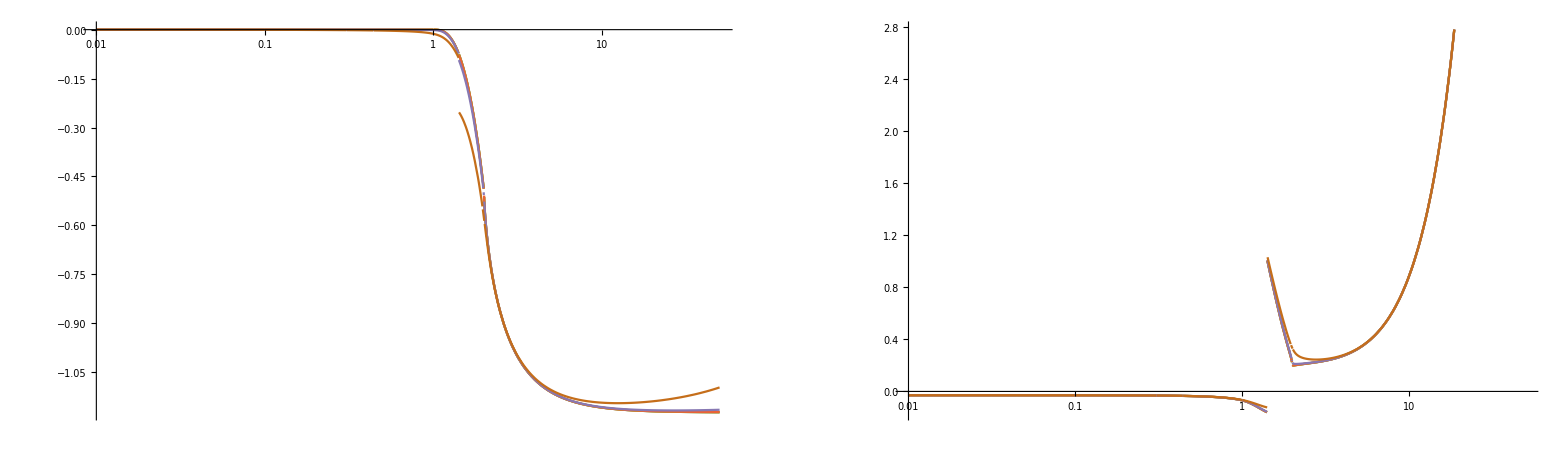

```mathematica
With[{ε=10^Range[-5,-1]},GraphicsRow[{LogLinearPlot[{Im[IVecRen[ω,22/100,1,1,2]]
,Evaluate[Im[IVecRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,0.5*10^2},WorkingPrecision->30],LogLinearPlot[{Re[IVecRen[ω,22/100,1,1,2]],Evaluate[Re[IVecRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,0.5*10^2},WorkingPrecision->30]},ImageSize->1600]]
```

Analytic continuation is correct!

#### Dirac Scalar Part

This part represents all terms in the diagram prop. to unity and will after the spectral integrations yield the relevant expression B (p^2).

```mathematica
IScalE[p_,αs_,λA_,λ_,μ_] := -(8 αs (-3 (-2+Log[λ]+(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+(-λ^2+λA^2) Log[λ/λA])/p^2+Log[λA])+Log[4 ⅇ^-EulerGamma π μ^2]))/π
IScalCont[ω_,αs_,λA_,λ_,μ_] := -1/π 8 αs (-3 (-2+Log[λ]-(√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2) ArcCoth[(λ^2+λA^2-ω^2)/(√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2))]+(-λ^2+λA^2) Log[λ/λA])/ω^2+Log[λA])+Log[4 ⅇ^-EulerGamma π μ^2])
IScalRenE[p_,αs_,λA_,λ_,μ_]:= IScalE[p,αs,λA,λ,μ] - IScalE[μ,αs,λA,λ,μ] (*- ((p^2-μ^2)/2/μ)(D[IScalE[q,αs,λA,λ,μ],q]/.{q->μ})*) (*Don't need to substract higher order terms!!*)
IScalRen[ω_,αs_,λA_,λ_,μ_]:= IScalRenE[-I*ω,αs,λA,λ,μ]
```

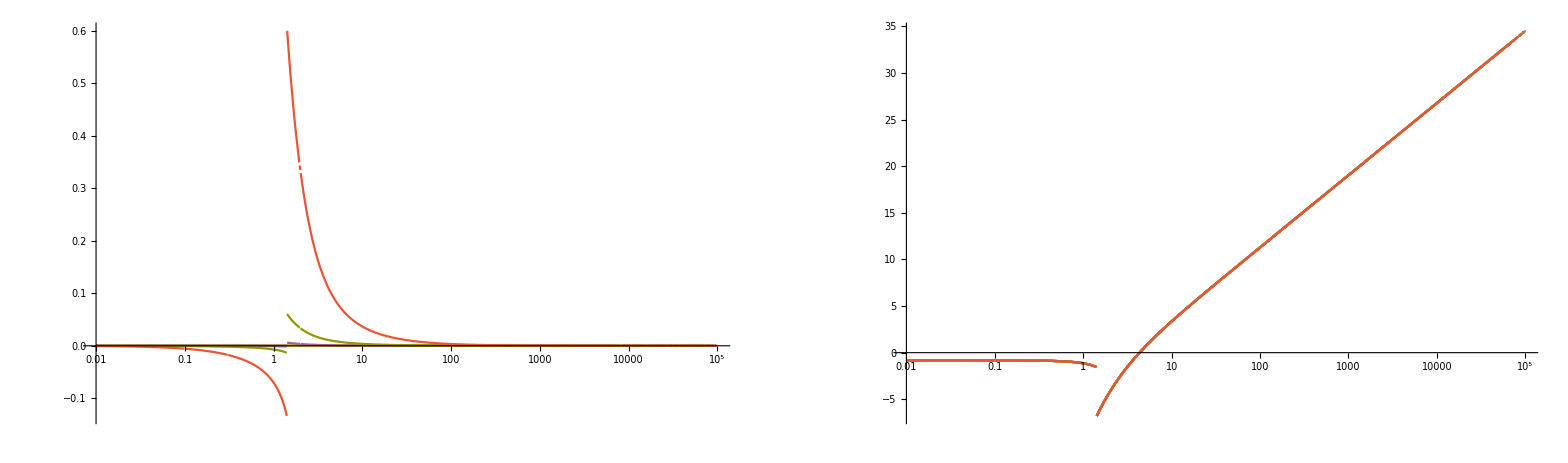

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[IScalRen[ω,22/100,1,1,2]],Evaluate[Im[IScalRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,10^5},WorkingPrecision->30, PlotRange->All],LogLinearPlot[{Re[IScalRen[ω,22/100,1,1,2]],Evaluate[Re[IScalRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,10^5},WorkingPrecision->30]},ImageSize->1600]]
```

### Spectral Regularization

Vector Part :

```mathematica
quarkSEVecReg[ω_,αs_,λA_,λ_,gluSpecFunc_,quarkSpecFunc1_]:=With[{μ=2},λA*λ/π^2*gluSpecFunc[λA]*quarkSpecFunc1[λ]*IVecRen[ω,αs,λA,λ,μ]]

quarkSEVecRegE[p_,αs_,λA_,λ_,gluSpecFunc_,quarkSpecFunc1_]:=With[{μ=2},λA*λ/π^2*gluSpecFunc[λA]*quarkSpecFunc1[λ]*IVecRenE[p,αs,λA,λ,μ]]

(*ATTENTION: Need to check whats the correct value of λ for the pole contributions*)
quarkSEVecRegPole[ω_,αs_,λA_,λ_,gluSpecFunc_]:=With[{μ=2},λA/π*gluSpecFunc[λA]*IVecRen[ω,αs,λA,λ,μ]]
			
quarkSEVecRegPoleE[p_,αs_,λA_,λ_,gluSpecFunc_]:=With[{μ=2},λA/π*gluSpecFunc[λA]*IVecRenE[p,αs,λA,λ,μ]]

(*Need to adapt to correct pole position -> see below*)

DquarkSEp0VecRegE[αs_,λA_,λ_,gluSpecFunc_,quarkSpecFunc1_]:=With[{μ=2},λA*λ/π^2*gluSpecFunc[λA]*quarkSpecFunc1[λ]*
(D[IVecE[q,αs,λA,λ,μ],q]/.{q->10^-8}/(2*10^-8)-1/(2μ)*D[IVecE[q,αs,λA,λ,μ],q]/.{q->μ})]

DquarkSEp0VecRegPoleE[αs_,λA_,gluSpecFunc_]:= With[{μ=2,λ=λRange[[1]]},4π*αs*λA/π*gluSpecFunc[λA]*(D[IVecE[q,αs,λA,λ,μ],q]/.{q->10^-8}/(2*10^-8)-1/(2μ)*D[IVecE[q,αs,λA,λ,μ],q]/.{q->μ})]
```

Scalar Part:

```mathematica
quarkSEScalReg[ω_,αs_,λA_,λ_,gluSpecFunc_,quarkSpecFunc2_]:=With[{μ=2},λA*λ/π^2*gluSpecFunc[λA]*quarkSpecFunc2[λ]*IScalRen[ω,αs,λA,λ,μ]]

quarkSEScalRegE[p_,αs_,λA_,λ_,gluSpecFunc_,quarkSpecFunc2_]:=With[{μ=2},λA*λ/π^2*gluSpecFunc[λA]*quarkSpecFunc2[λ]*IScalRenE[p,αs,λA,λ,μ]]

quarkSEScalRegPole[ω_,αs_,λA_,λ_,gluSpecFunc_]:=With[{μ=2},λA/π*gluSpecFunc[λA]*IScalRen[ω,αs,λA,λ,μ]]

quarkSEScalRegPoleE[p_,αs_,λA_,λ_,gluSpecFunc_]:=With[{μ=2},λA/π*gluSpecFunc[λA]*IScalRenE[p,αs,λA,λ,μ]]

(*Same here*)
DquarkSEp0ScalRegE[αs_,λA_,λ_,gluSpecFunc_,quarkSpecFunc2_]:=With[{μ=2},λA*λ/π^2*gluSpecFunc[λA]*quarkSpecFunc2[λ]*
(D[IScalE[q,αs,λA,λ,μ],q]/.{q->10^-8}/(2*10^-8)-1/(2μ)*D[IScalE[q,αs,λA,λ,μ],q]/.{q->μ})]

DquarkSEp0ScalRegPoleE[αs_,λA_,gluSpecFunc_]:= With[{μ=2,λ=λRange[[1]]},4π*αs*λA/π*gluSpecFunc[λA]*(D[IScalE[q,αs,λA,λ,μ],q]/.{q->10^-8}/(2*10^-8)-1/(2μ)*D[IScalE[q,αs,λA,λ,μ],q]/.{q->μ})]
```

## Input Gluon Spectral Function

Needs to be rescaled by a factor of 52/100 to match with lattice data, Jan told me this.

```mathematica
GluonProp[p_,rescaling_ :52/100]:=rescaling*(2.6593023336775623 (0.24101744007732523 p^2-1.3080381149734166 p^4+0.4540243805575766 √(p^2)+3.102572099727779 (p^2)^(3/2)+0.6370104930721061 (p^2)^(5/2)) (1/(0.7223337923370855+(0.10014054778030819+p)^2))^1.940947667539462 (1/(0.7223006948918959+(0.10016935623821763+p)^2))^1.6111555266576754 (1/(5.603766404618137+(1.1510177570696811+p)^2))^0.2962151724379364 (1/(12.971529659828924+(1.220130041357888+p)^2))^0.168591834497177 (1/(5.9553300841709165+(1.5564010970324915+p)^2))^1.8976530064403432)/((p^2)^0.1425720117966328 (1/(6.359002348225766+(2.364448929855074+p)^2))^2.545863533505827 Log[1+0.32634744468212906 p^2]^0.22278738808344056)
```

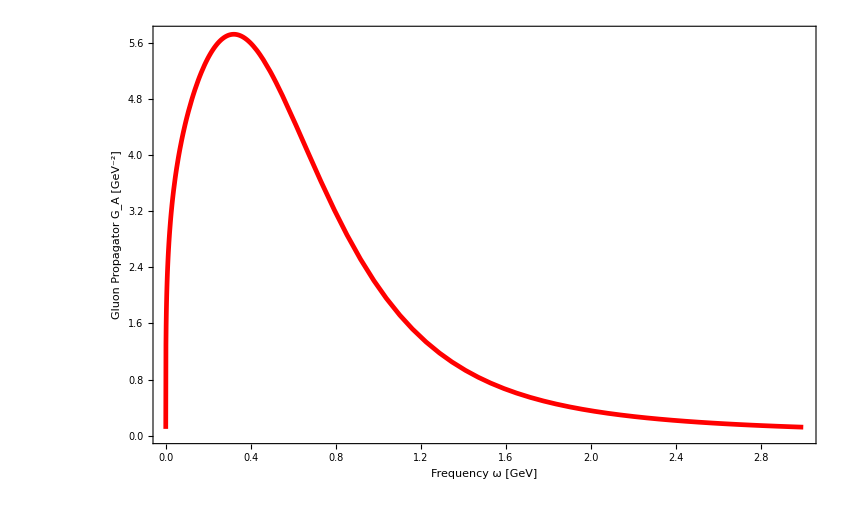

```mathematica
Plot[GluonProp[p],
{p,0,3},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
(*PlotRange->{{0.35,1.45},{-15000,24000}},*)
FrameLabel->{"Frequency ω [GeV]", "Gluon Propagator G_A [GeV^-2]"},
PlotStyle->{Directive[Red,Thickness[0.004]]}
]
```

```mathematica
GluonPropDressing[p_, rescaling_ :52/100]:= p^2*GluonProp[p, rescaling]
```

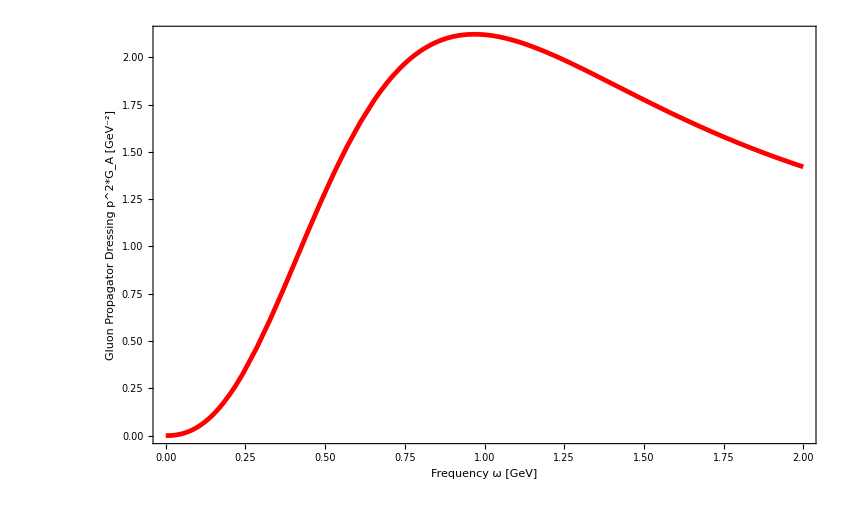

```mathematica
Plot[GluonPropDressing[p],
{p,0,2},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
(*PlotRange->{{0.35,1.45},{-15000,24000}},*)
FrameLabel->{"Frequency ω [GeV]", "Gluon Propagator Dressing p^2*G_A [GeV^-2]"},
PlotStyle->{Directive[Red,Thickness[0.004]]}
]
```

Extracting the spectral function from the propagator data:

```mathematica
GluonSpecFunc[ω_,ε_ :5*10^-8, rescaling_ : 52/100]:=-2Im[GluonProp[I*ω+ε, rescaling]] (*has to be rescaled rescaled to match with lattice date, Jan told me this, we did this above by rescaling the Gluon Propagator*)
```

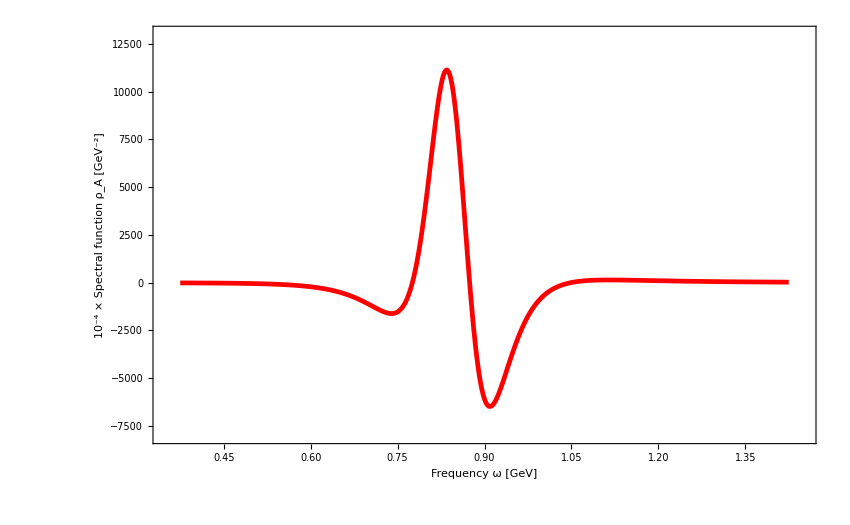

```mathematica
Plot[GluonSpecFunc[ω],
{ω,0.375,1.425},
ImageSize->850,Frame->True,Exclusions->None,Axes->None,
PlotRange->{{0.35,1.45},{-8000,13000}},
FrameLabel->{"Frequency ω [GeV]", "10^-4 × Spectral function ρ_A [GeV^-2]"},
PlotStyle->{Directive[Red,Thickness[0.004]]}
]
```

## Iterative Spectral Functions - Initialization

Here we finally set up the numerics to compute the numerical spectral functions.

### Auxiliary Functions

The functions defined below are used later on to perform the discretization and interpolation of the respective integrands.

```mathematica
intPolFunc[w_,gridvals_,grid_]:=f[w]/.{f -> Interpolation[
Table[{grid[[j]],gridvals[[j]]},{j,Length[grid]}],Method->"Spline",InterpolationOrder->2
] 
}
(*Below grid function creates a custom grid refining a set (list) of input points and attaching a tail of specifiable length*)
gridFunc[pointsToRefine_,start_,tailstart_,tailend_,smallStep_,step_,largeStep_]:=(Do[If[Length[pointsToRefine]==1, grid=Join[Range[start,pointsToRefine[[i]]-step,step],Range[pointsToRefine[[i]]-(step-smallStep),pointsToRefine[[i]]+(step-smallStep),smallStep],Range[pointsToRefine[[i]]+step,tailstart,step],Range[tailstart+largeStep,tailend,largeStep]],If[i==1,grid=Join[Range[start,pointsToRefine[[i]]-step,step],Range[pointsToRefine[[i]]-(step-smallStep),pointsToRefine[[i]]+(step-smallStep),smallStep]],If[i==Length[pointsToRefine],grid=Join[grid,Range[pointsToRefine[[i-1]]+step,pointsToRefine[[i]]-step,step],Range[pointsToRefine[[i]]-(step-smallStep),pointsToRefine[[i]]+(step-smallStep),smallStep],Range[pointsToRefine[[i]]+step,tailstart,step],Range[tailstart+largeStep,tailend,largeStep]],grid=Join[grid,Range[pointsToRefine[[i-1]]+step,pointsToRefine[[i]]-step,step],Range[pointsToRefine[[i]]-(step-smallStep),pointsToRefine[[i]]+(step-smallStep),smallStep]]]]],
{i,Length[pointsToRefine]}];
grid)
CheckNonNum[list_]:=Select[list,!MemberQ[Select[list,NumericQ],#]&]
SetAttributes[DeleteListElements,HoldAll]
DeleteListElements[elem_,lists_]:=
Scan[
Function[x,
If[Length[x]≥elem,
Unevaluated[x]=Delete[x,elem],
Print["Length of " ,Unevaluated[x]," is less than ",elem]
],{HoldAll}
]
,lists
]
```

### Discretization and Interpolation

#### Discretize Integrand (Compute values on respective grid point) --- NOT INCLUDED IN THESIS AND NOT COMPLETE ---

```mathematica
quarkSEVecTbl={};
quarkSEVecTblE={};
DquarkSEVecTblE = {};
```

Gridsize for discretization (maybe needs to be adapted)

```mathematica
ωRange=10^Range[-5,4,1/10];
λRange=10^Range[-5,4,1/20];
```

#### Euclidean

Adapt to full expression:

```mathematica
discrT1=AbsoluteTiming[  
Do[
Do[
Do[

tempRes=With[{αs=22/100,μ=2},N[IVecE[ωRange[[i]],αs,λRange[[j]],λRange[[k]],μ],30]];

If[k==1,

tempResLim=With[{αs=22/100,μ=2},N[IVecE[ωRange[[i]],αs,λRange[[j]],λRange[[k]]/100,μ],30]];

AppendTo[
quarkSEVecTblE,{{ωRange[[i]],λRange[[j]],0},tempResLim}
];
AppendTo[
quarkSEVecTblE,{{ωRange[[i]],λRange[[j]],λRange[[k]]},tempRes}
];,

AppendTo[
quarkSEVecTblE,{{ωRange[[i]],λRange[[j]],λRange[[k]]},tempRes}
];
]

, {k,Length[λRange]}]
, {j, Length[λRange]}]
, {i, Length[ωRange]}]
][[1]];
Print[StringForm["Duration: `` seconds)",discrT1]];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(44 (-1/4+«10»+1/2 (-10000000000 (-3/10000000000+100000 Power[«2»])+10000000000 (1/10000000000+100000 Power[«2»])) Log[16 ⅇ^-EulerGamma π]))/(75 π).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(44 («1»))/(75 π).

General::stop: Further output of N::meprec will be suppressed during this calculation.

$Aborted

Duration: discrT1 seconds)

#### Minkowski

Adapt to full expression :

```mathematica
Do[
Do[
Do[

tempRes=With[{αs=22/100,μ=2},N[IVecCont[ωRange[[i]],αs,λRange[[j]],λRange[[k]],μ],30]];

If[k==1,

tempResLim=With[{αs=22/100,μ=2},N[IVecCont[ωRange[[i]],αs,λRange[[j]],λRange[[k]]/100,μ],30]];

AppendTo[
quarkSEVecTbl,{{ωRange[[i]],λRange[[j]],0},tempResLim}
];
AppendTo[
quarkSEVecTbl,{{ωRange[[i]],λRange[[j]],λRange[[k]]},tempRes}
];,

AppendTo[
quarkSEVecTbl,{{ωRange[[i]],λRange[[j]],λRange[[k]]},tempRes}
];
]

, {k,Length[λRange]}]
, {j, Length[λRange]}]
, {i, Length[ωRange]}]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

#### Euclidean Derivative

```mathematica
Do[
Do[

tempRes=With[{αs=22/100,μ=2},N[DIVecE[μ,αs,λRange[[j]],λRange[[k]],μ],30]];

If[k==1,

tempResLim=With[{αs=22/100,μ=2},N[DIVecE[μ,αs,λRange[[j]],λRange[[k]]/100,μ],30]];

AppendTo[
DquarkSEVecTblE,{{λRange[[j]],0},tempResLim}
];
AppendTo[
DquarkSEVecTblE,{{λRange[[j]],λRange[[k]]},tempRes}
];,

AppendTo[
DquarkSEVecTblE,{{λRange[[j]],λRange[[k]]},tempRes}
];
]

, {k,Length[λRange]}]
, {j, Length[λRange]}]
```

#### Interpolation

```mathematica
quarkSEVecIntPol=Interpolation[quarkSEVecTbl];
quarkSEVecIntPolE=Interpolation[quarkSEVecTblE];
DquarkSEVecIntPolE=Interpolation[DquarkSEVecTblE];
```

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

### Iterating Functions

Now we can finally define the iterated functions, that will later be used to extract the spectral functions -> Changed dressings to our conventions from A and B to Zq and Mq:

```mathematica
AIter[ω_,quarkSEVecIter_ ]:=1-ⅈ/24*quarkSEVecIter[ω] (*factor of 1/24 from projections onto G_A*)
AIterE[p_,quarkSEVecIterE_]:=1-ⅈ/24*quarkSEVecIterE[p]

BIter[ω_, mq_, quarkSEScalIter_ ]:=mq-1/24*quarkSEScalIter[ω]
BIterE[p_, mq_, quarkSEScalIterE_]:=mq-1/24*quarkSEScalIterE[p]

ρ1[ω_, ZqIter_, MqIter_]:= 2*Im[-ⅈ(ZqIter[ω]/(-ω^2 + MqIter[ω]^2))]
ρ2[ω_, ZqIter_, MqIter_]:= 2*Im[ZqIter[ω]*MqIter[ω]/(-ω^2 + MqIter[ω]^2)]
```

### Initial Spectral Functions

Gluon (always the same input, maybe also test some scaling solutions later ):

```mathematica
Clear[ω, ρA]
```

```mathematica
ρADecoupling = Evaluate[GluonSpecFunc];
```

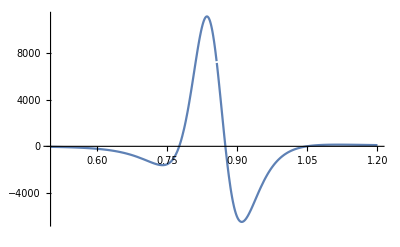

```mathematica
Plot[ρADecoupling[λA], {λA,0.5,1.2}, PlotRange->All]
```

Quarks : (Talked to Jan, maybe we need some damping of the massive delta function at higher momenta -> after first trials, skip that, check χSB ansatz below)

```mathematica
FindMaximum[ρADecoupling[λA],{λA,0.85}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{11130.5,{λA→0.834844}}

```mathematica
Clear[λ,mq, ρ1Init, ρ2Init]
```

```mathematica
ρ1Init[λ_, mq_]:= (2π ⅈ) * DiracDelta[λ-mq]/(2λ);
ρ2Init[λ_, mq_]:=(-2π*mq) * DiracDelta[λ-mq]/(2λ);
```

Second ansatz (meeting  with Jan - 31.05.21 - not yet tested)

```mathematica
ρ1χSB[λ_, mq_]:= (2π ⅈ) * DiracDelta[λ-mq]/(2λ); (*maybe need different ansatz here inspired by results for classical initial guess*)
ρ2χSB := 0
```

### Lists for Iteration

Here we define the lists where all relevant quantities are stored for every iteration step.

```mathematica
(*Store results of the numerical evaluation of the spectral integrals*)
quarkSEVecIters = {};
quarkSEVecItersE = {}; 

quarkSEScalIters = {};
quarkSEScalItersE = {};

Poles ={}; 
Residues ={};

ZqIters={};
ZqItersE={};

MqIters={};
MqItersE={};

(*Extract and append result from iteration to be able to access i-1st element as input for ith iteration*)
SpecFuncsρ1={};
SpecFuncsρ2={};
```

### 0th iteration, Test

#### Computing A for the initial guess of ρ1

```mathematica
Clear[ω,p,λA,λ]
```

```mathematica
ATest[p_,αs_,μ_] := With [{mq=1}, 1-ⅈ*NIntegrate[(ⅈ*λA*ρADecoupling[λA]IVecRenE[p,αs,λA,mq,μ])/mq,{λA,10^-2,10^4},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3]]
ATestTbl = Table[{p,ATest[p,22/100,2]}, {p,10^Range[-3,4,1/20]}]
ATestInt = Interpolation[ATestTbl]
```

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λA near {λA} = {312.030319282961196812153007251}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λA near {λA} = {312.030319282961196812153007251}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λA near {λA} = {312.030319282961196812153007251}. NIntegrate obtained 0 and 0 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1/1000,1},{1/(100 10^(19/20)),1},{1/(100 10^(9/10)),1},{1/(100 10^(17/20)),1},{1/(100 10^(4/5)),1},{1/(100 10^(3/4)),1},{1/(100 10^(7/10)),1},{1/(100 10^(13/20)),1},{1/(100 10^(3/5)),1},{1/(100 10^(11/20)),1},{1/(100 √10),1},{1/(100 10^(9/20)),1},{1/(100 10^(2/5)),1},{1/(100 10^(7/20)),1},{1/(100 10^(3/10)),1},{1/(100 10^(1/4)),1},{1/(100 10^(1/5)),1},{1/(100 10^(3/20)),1},{1/(100 10^(1/10)),1},{1/(100 10^(1/20)),1},{1/100,1},{1/(10 10^(19/20)),1},{1/(10 10^(9/10)),1},{1/(10 10^(17/20)),1},{1/(10 10^(4/5)),1},{1/(10 10^(3/4)),1},{1/(10 10^(7/10)),1},{1/(10 10^(13/20)),1},{1/(10 10^(3/5)),1},{1/(10 10^(11/20)),0.903124301285790456473747201169},{1/(10 √10),0.903155220546255612614121526891},{1/(10 10^(9/20)),0.90319413200217815546987942691},{1/(10 10^(2/5)),0.903243097098473756238402031056},{1/(10 10^(7/20)),0.903304706407075534284046566518},{1/(10 10^(3/10)),0.903382213930411027504050044077},{1/(10 10^(1/4)),0.903479704608748153463631683512},{1/(10 10^(1/5)),0.903602302719011407866466100009},{1/(10 10^(3/20)),0.903756430319971213822850066497},{1/(10 10^(1/10)),0.903950126448661079677205303207},{1/(10 10^(1/20)),0.904193439261593232820339916167},{1/10,0.904498904472366305692972218325},{1/10^(19/20),0.904882123793432243222549054367},{1/10^(9/10),0.905362455857504991906950339311},{1/10^(17/20),0.905963828006647877087306238309},{1/10^(4/5),0.906715668419458988454990206821},{1/10^(3/4),0.907653941319092708530823956534},{1/10^(7/10),0.908822239137104258761923019659},{1/10^(13/20),0.9102728385040384878955866807239},{1/10^(3/5),0.9120675540457085751611036640375},{1/10^(11/20),0.9142781162369630297073953669856},{1/(√10),0.9169856488648281198442586279433},{1/10^(9/20),0.9202786254449947212793502653695},{1/10^(2/5),0.9242484548176453049913305680866},{1/10^(7/20),0.9289816283109942895444550495822},{1/10^(3/10),0.934547254431467968661734773885},{1/10^(1/4),0.9409789964422589190047619495552},{1/10^(1/5),0.9482512005102857627475777532719},{1/10^(3/20),0.9562507061311702332059406575842},{1/10^(1/10),0.9647487968812122737422694579676},{1/10^(1/20),0.9733818734453891008356881590389},{1,0.9816539166124404327414330301795},{10^(1/20),0.9889766429938368624280869673515},{10^(1/10),0.99476136254998590702958226876735},{10^(3/20),0.99856718839568657076826702119163},{10^(1/5),1.00029332564341753645894703280365},{10^(1/4),1.00038373784172596752152617362787},{10^(3/10),1.00000049816467839368918125089796032},{10^(7/20),1.0011254724217724743658243463039},{10^(2/5),1.0065792355501775059917744383489},{10^(9/20),1.019969902194353342982419907966},{√10,1.04562599025026715416534248251},{10^(11/20),1.088567124714589388614990752942},{10^(3/5),1.15456208741670149307853504721},{10^(13/20),1.25030203350614362470415870595},{10^(7/10),1.38369795440025211032814718277},{10^(3/4),1.56430164216007395854462818869},{10^(4/5),1.80385019135653877168733737156},{10^(17/20),2.1169428882722407303754148649},{10^(9/10),2.52187213720796492151381459579},{10^(19/20),3.04164477325517425856160965677},{10,3.70524485944145566474022046921},{10 10^(1/20),4.54920507190631445181790744375},{10 10^(1/10),5.61957213587842530217735650251},{10 10^(3/20),6.97437245324430432182661024953},{10 10^(1/5),8.68671141381956415974694053186},{10 10^(1/4),10.8486729729203387419289285824},{10 10^(3/10),13.5762274933998415618056552929},{10 10^(7/20),17.0154119029677325707750389236},{10 10^(2/5),21.3501093266778466731143266796},{10 10^(9/20),26.811844506888594945900319141},{10 √10,33.6921161344451266441995328154},{10 10^(11/20),42.3579229936025150654744378521},{10 10^(3/5),53.2713107513715859483045208991},{10 10^(13/20),67.0139817104782374386538840926},{10 10^(7/10),84.3182700314982697125747176465},{10 10^(3/4),106.106151109487211262195168704},{10 10^(4/5),133.538338057805417977343029098},{10 10^(17/20),168.076097322924646821326595646},{10 10^(9/10),211.559068657675096359528008743},{10 10^(19/20),266.303234701043946177496617038},{100,335.224257399190771027808197511},{100 10^(1/20),421.992749382946729215679708956},{100 10^(1/10),531.229749072765091922626592732},{100 10^(3/20),668.752809279112330350438816286},{100 10^(1/5),841.885804420664033208188970858},{100 10^(1/4),1059.84895473198351657889203604},{100 10^(3/10),1334.24983767963664810203160575},{100 10^(7/20),1679.70153474248527694707396602},{100 10^(2/5),2114.60090292598929586453270692},{100 10^(9/20),2662.10800909510057893806787388},{100 √10,3351.3798634149883766512765057},{100 10^(11/20),4219.12290297227087015568600085},{100 10^(3/5),5311.54779854282786065135771761},{100 10^(13/20),6686.83054824689684436782718249},{100 10^(7/10),8418.20962318738823222147853018},{100 10^(3/4),10597.8875312284725064231679068},{100 10^(4/5),13341.9402443210481448875167423},{100 10^(17/20),16796.4996131464223936405727111},{100 10^(9/10),21145.5327685611299550869281325},{100 10^(19/20),26620.6419537277410709417228784},{1000,33513.3983106434729050512171208},{1000 10^(1/20),42190.8637538296781374921190952},{1000 10^(1/10),53115.1462346286328284407695057},{1000 10^(3/20),66868.0037431965571740699451765},{1000 10^(1/5),84181.8261962954042641219237783},{1000 10^(1/4),105978.637870794528410485836468},{1000 10^(3/10),133419.198558438687134520206393},{1000 10^(7/20),167964.818257451754916612869707},{1000 10^(2/5),211455.177258732505532618292752},{1000 10^(9/20),266206.295830011962175769520759},{1000 √10,335133.870740895374891203919085},{1000 10^(11/20),421908.546748477412168049510056},{1000 10^(3/5),531151.391816312343522445113437},{1000 10^(13/20),668679.985834921465787248118882},{1000 10^(7/10),841818.22796553991603219824271},{1000 10^(3/4),1.05978636097784700402880376942×10^6},{1000 10^(4/5),1.33419198279987203205871625799×10^6},{1000 10^(17/20),1.67964819343557395558005462486×10^6},{1000 10^(9/10),2.11455179582752948876731784118×10^6},{1000 10^(19/20),2.66206299269838629895564398267×10^6},{10000,3.35133875180037022624067578824×10^6}}

InterpolatingFunction[…]

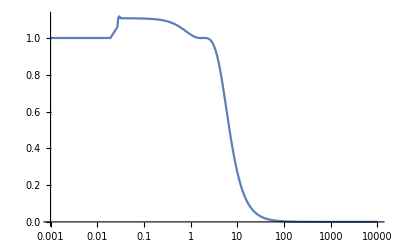

```mathematica
LogLinearPlot[{1/ATestInt[p](*, p^2*)},{p,10^-3,10^4}]
```

```mathematica
FindRoot[ATestInt[p] == 0, {p,0.1}]
```

InterpolatingFunction::dmval: Input value {-5.22689} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::jsing: Encountered a singular Jacobian at the point {p} = {-5.22689}. Try perturbing the initial point(s).

{p→-5.22689}

#### Computing B for the initial guess of ρ2

```mathematica
BTest[p_,αs_,μ_] := With [{mq=1}, mq - NIntegrate[(λA*ρADecoupling[λA]IScalRenE[p,αs,λA,mq,μ]/mq),{λA,10-2,10^5},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3]]
BTestTbl = Table[{p,BTest[p, 22/100, 2]}, {p,10^Range[-3,4,1/10]}]
BTestInt = Interpolation[BTestTbl]
```

NIntegrate::precw: The precision of the argument function (-2.76567 λA Im[((0.241017 (1/20000000+Times[«2»])^2-1.30804 (1/20000000+Times[«2»])^4+0.454024 √(Plus[«2»]^2)+3.10257 (Plus[«2»]^2)^(3/2)+0.63701 (Plus[«2»]^2)^(5/2)) (1/(«19»+«1»))^1.94095 («1»)^(«19») («1»)^(«19») (1/(«1»))^(«18») (1/(«19»+(«1»)^2))^1.89765)/((1/(6.359+Plus[«2»]^2))^2.54586 ((1/20000000+ⅈ λA)^2)^0.142572 Log[1+0.326347 Power[«2»]]^0.222787)] (-(44 (Log[16 ⅇ^Times[«2»] π]-3 (-2+1000000 Plus[«2»]+Log[λA])))/(25 π)+(44 (Log[16 ⅇ^Times[«2»] π]-3 (-2+1/4 Plus[«2»]+Log[λA])))/(25 π))) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-2.76567 λA Im[((0.241017 (1/20000000+Times[«2»])^2-1.30804 (1/20000000+Times[«2»])^4+0.454024 √(Plus[«2»]^2)+3.10257 (Plus[«2»]^2)^(3/2)+0.63701 (Plus[«2»]^2)^(5/2)) (1/(«19»+«1»))^1.94095 ((«1»«1»)^(«19») «1» (1/(«1»))^(«18») (1/(«19»+(«1»)^2))^1.89765)/((1/(6.359+Plus[«2»]^2))^2.54586 ((1/20000000+ⅈ λA)^2)^0.142572 Log[1+0.326347 Power[«2»]]^0.222787)] ((44 (Log[16 ⅇ^Times[«2»] π]-3 (-2+1/4 Plus[«2»]+Log[λA])))/(25 π)-(44 (Log[16 ⅇ^Times[«2»] π]-3 (-2+100000 Power[«2»] Plus[«2»]+Log[λA])))/(25 π))) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{{1/1000,0.9885589629645671696482995753694},{1/(100 10^(9/10)),0.9885589645549933768258865359886},{1/(100 10^(4/5)),0.9885589671492298601376419183201},{1/(100 10^(7/10)),0.9885589713199283440080773404162},{1/(100 10^(3/5)),0.9885589779708545090922894588407},{1/(100 √10),0.9885589886035257764226698323402},{1/(100 10^(2/5)),0.988559005480643962680214703988},{1/(100 10^(3/10)),0.98855903222724693788933352563},{1/(100 10^(1/5)),0.9885590746648971934664032559743},{1/(100 10^(1/10)),0.9885591419597050242679209996913},{1/100,0.9885592486347807437881104602667},{1/(10 10^(9/10)),0.9885594177204698594436131688438},{1/(10 10^(4/5)),0.9885596857168863505614421270308},{1/(10 10^(7/10)),0.9885601104811543778474476731674},{1/(10 10^(3/5)),0.988560783683695155269392088011},{1/(10 √10),0.9885618506568174453114580033004},{1/(10 10^(2/5)),0.9885635416904227067321914878644},{1/(10 10^(3/10)),0.9885662217980275680157053881467},{1/(10 10^(1/5)),0.9885704694628891102115296115263},{1/(10 10^(1/10)),0.9885772014942850498763496602676},{1/10,0.9885878708702583181567039032836},{1/10^(9/10),0.9886047802568083255895413588385},{1/10^(4/5),0.9886315787272629501796118105335},{1/10^(7/10),0.9886740486633135487729682718054},{1/10^(3/5),0.9887413520074873344224059714799},{1/(√10),0.988848003109872097018624880692},{1/10^(2/5),0.9890169897627533097672244143847},{1/10^(3/10),0.9892847052444625127235743431739},{1/10^(1/5),0.9897087289925505586379290335038},{1/10^(1/10),0.9903800678929240312123366291218},{1,0.991442332737639228635222155785},{10^(1/10),0.99312157413780316388867909515165},{10^(1/5),0.99577220076426645141819807311242},{10^(3/10),0.9999464325971568066450748766906224},{10^(2/5),1.0064964676301088084408658655157},{√10,1.016718139299185413036561421535},{10^(3/5),1.032538346398903985620107765396},{10^(7/10),1.056729533588261708630281917926},{10^(4/5),1.093097590324414423456487652704},{10^(9/10),1.14654210398787082325894299774},{10,1.2228660770050734630581086883},{10 10^(1/10),1.32827139409552296405075872943},{10 10^(1/5),1.46862576176582545579715432977},{10 10^(3/10),1.64873025933712928940542116648},{10 10^(2/5),1.87182677370300570724683487185},{10 √10,2.13945401365249219889501537559},{10 10^(3/5),2.45160540010004138880096016167},{10 10^(7/10),2.80706143083303394428467872534},{10 10^(4/5),3.20377134792111832049494512343},{10 10^(9/10),3.63920134664474033865582046981},{100,4.11061121271800343147990455841},{100 10^(1/10),4.61525229750861087976387666528},{100 10^(1/5),5.15049545192733438149241054626},{100 10^(3/10),5.71390512880462959607114084667},{100 10^(2/5),6.30327347568861422215722286812},{100 √10,6.91662848035722621530206608172},{100 10^(3/5),7.55222577196530088834825512774},{100 10^(7/10),8.20853133059626621244216717879},{100 10^(4/5),8.88419994074905821226310488745},{100 10^(9/10),9.57805251699757010595586360433},{1000,10.2890541523657985074367346949},{1000 10^(1/10),11.01629389970563244950696068},{1000 10^(1/5),11.758966738305928652624007012},{1000 10^(3/10),12.5163578329038720268972397133},{1000 10^(2/5),13.2878289891701402443034327341},{1000 √10,14.0728070986225402178935895793},{1000 10^(3/5),14.8707743110382207015441320343},{1000 10^(7/10),15.6812596478681358186894695137},{1000 10^(4/5),16.5038317571342443292296429432},{1000 10^(9/10),17.3380924940460972812386203192},{10000,18.1836709791478832569734619585}}

InterpolatingFunction[…]

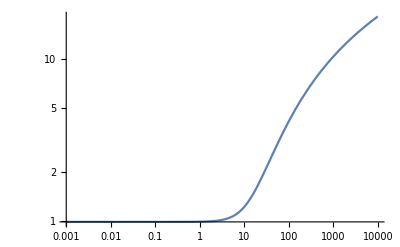

```mathematica
LogLogPlot[{Abs[BTestInt[p]]},{p,10^-3,10^4}]
```

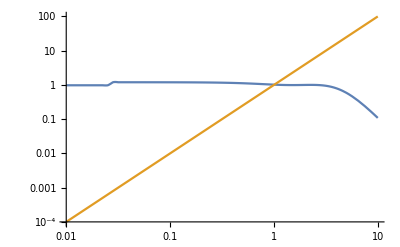

```mathematica
LogLogPlot[{Abs[BTestInt[p]^2/ATestInt[p]^2],p^2},{p,10^-2,10^1}]
```

```mathematica
FindRoot[BTestInt[p]^2/ATestInt[p]^2 + p^2== 0, {p,1}]
```

InterpolatingFunction::dmval: Input value {-0.0808477} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00726483} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{p→0.0239742}

```mathematica
{p->0.0239741935326605}
```

{p→0.0239742}

```mathematica
1/(1 + (BTestInt[0.0239741935326605]/ATestInt[0.0239741935326605])*(D[(BTestInt[q]^2/ATestInt[q]^2) ,q]/.{q->0.0239741935326605})/0.0239741935326605)
```

-1.03348

### Loading current data to initialize the iteration

```mathematica
<<realtime_quark_specfuncs_monday1.mx;
```

## Iteration 1 (“Classical Initial Guess”)

```mathematica
(*CHECK IF THE LISTS ARE EMPTY BEFORE STARTING A NEW ITERATION!!!*)
```

```mathematica
Do[
With[{mq=1/100,αs=22/100,λAmin=10^-3,λAmax=10^2,λmin=10^-3,λmax=10^2,μ=2,momRange=10^Range[-2,1,1/2]}, (*Peak of Gluon SpecFunc = 1 GeV -> are interested in Mq of the order MeV -> 1/100*)

(*Gluon spectral function does not need to be updated, its simply given by the input data*)
 ρATmp=ρADecoupling;

(*Specifying initial conditions*)
If[i==1, 

(*Use "classical" spectral function (= delta peak) as initial guess for the first iteration, probably causes problems*)
ρ1Tmp:= ρ1Init[λ,mq];
ρ2Tmp:=  ρ2Init[λ,mq];

(* Initial Pole Position + Residues*) 
PoleTmp =mq;  
ResidueTmp= 1;  
(*I computed these values above, just for checking*)
 
Print["Initial Pole: " ,PoleTmp];
Print["Initial Residue: " ,ResidueTmp]; , (*Comma VERY IMPORTANT, here ends the initialization for i=1!!!*)

(*Access updated relevant quantities as the last entry of the respective list for i>1*)
ρ1DiscrTmp = SpecFuncsρ1[[-1]];
ρ2DiscrTmp = SpecFuncsρ2[[-1]];

ρ1Tmp= Interpolation[ρ1DiscrTmp];
ρ2Tmp= Interpolation[ρ2DiscrTmp];

PoleTmp = Poles[[-1]];
ResidueTmp  = Residues[[-1]];
Print["Test for subsequent iters: ",  ρ1DiscrTmp ];

];

(*Here the actual computations start*)
Quiet[
iterT=AbsoluteTiming[ 

Print["Computing Minkowski diagrams"];
AppendTo[
quarkSEVecIters,Table[
{ω,ResidueTmp*NIntegrate[quarkSEVecRegPole[ω,αs,λA,PoleTmp,ρATmp],{λA,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3](*+NIntegrate[quarkSEVecReg[ω,αs,λA,λ,ρATmp,ρ1Tmp],{λA,λAmin,λAmax},{λ,λmin,λmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]*)},{ω,momRange}
]
];
AppendTo[
quarkSEScalIters,Table[
{ω,ResidueTmp*NIntegrate[quarkSEScalRegPole[ω,αs,λA,PoleTmp,ρATmp],{λA,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3](*+NIntegrate[quarkSEScalReg[ω,αs,λA,λ,ρATmp,ρ2Tmp],{λA,λAmin,λAmax},{λ,λmin,λmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]*)},{ω,momRange}
]
];

Print["Computing Euclidean diagrams"];
AppendTo[
quarkSEVecItersE,Table[ 
{p,ResidueTmp*NIntegrate[quarkSEVecRegPoleE[p,αs,λA,PoleTmp,ρATmp],{λA,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3](*+NIntegrate[quarkSEVecRegE[p,αs,λA,λ,ρATmp,ρ1Tmp],{λA,λAmin,λAmax},{λ,λmin,λmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3]*)},{p,momRange}
]
];
AppendTo[
quarkSEScalItersE,Table[ 
{p,ResidueTmp*NIntegrate[quarkSEScalRegPoleE[p,αs,λA,PoleTmp,ρATmp],{λA,λAmin,λAmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3](*+NIntegrate[quarkSEScalRegE[p,αs,λA,λ,ρATmp,ρ2Tmp],{λA,λAmin,λAmax},{λ,λmin,λmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3]*)},{p,momRange}
]
];

Print["Computing Minkowski dressings"]; 
AppendTo[
ZqIters,Table[ 
{ω,1/ AIter[ω,Interpolation[quarkSEVecIters[[i]]]]},{ω,momRange}
]
];

AppendTo[
MqIters,Table[ 
{ω, BIter[ω,mq,Interpolation[quarkSEScalIters[[i]]]]/AIter[ω,Interpolation[quarkSEVecIters[[i]]]]},{ω,momRange}
]
];

Print["Computing Euclidean dressings"];
AppendTo[
ZqItersE,Table[ 
{p,1/ AIterE[p,Interpolation[quarkSEVecItersE[[i]]]]},{p,momRange}
]
];

AppendTo[
MqItersE,Table[ 
{p, BIterE[p,mq,Interpolation[quarkSEScalItersE[[i]]]]/AIterE[p,Interpolation[quarkSEVecItersE[[i]]]]},{p,momRange}
]
];

Print["Accessing the spectral functions"];
AppendTo[
SpecFuncsρ1,Table[ 
{ω,ρ1[ω, Interpolation[ZqIters[[i]]],  Interpolation[MqIters[[i]]]]},{ω,momRange}
]
];

AppendTo[
SpecFuncsρ2,Table[ 
{ω,ρ2[ω,Interpolation[ZqIters[[i]]],  Interpolation[MqIters[[i]]]]},{ω,momRange}
]
];

Print["Updating Pole Position + Residues"];
AppendTo[
Poles, p/.FindRoot[Interpolation[MqItersE[[i]]][p]^2 + p^2 == 0,{p, PoleTmp}]
];

Print["New pole at ", Poles[[-1]]];

AppendTo[
Residues,Re[1/(1 + (Interpolation[MqItersE[[-1]]][Poles[[-1]]]*D[Interpolation[MqItersE[[-1]]][q],q]/.{q->Poles[[-1]]})/Poles[[-1]])] 
];
Print["Updated residue ", Residues[[-1]]];
][[1]]; 
]

(*Store Results*)
(*DumpSave["realtime_quark_specfuncs_first_trials_overnight.mx",{
(*Diagrams*)
quarkSEVecIters,quarkSEVecItersE, quarkSEScalIters,quarkSEScalItersE,
	  (*Dressing functions*)
ZqIters, ZqItersE,
MqIters, MqItersE,
(*Poles & Residues*)
	  Poles, Residues,
	  (*Spectral functions*)
	 SpecFuncsρ1,SpecFuncsρ2
}];*)


(*How long did this iteration take?*)   
Print[StringForm["Iteration `` complete. (`` seconds)",i,iterT]];

(*Clean up the temporary variables*) 
Clear[ρ1DiscrTmp ,ρ2DiscrTmp ,ρ1Tmp,ρ2Tmp,PoleTmp ,ResidueTmp];
] ,
 {i,1,1}  ]
```

Initial Pole: 1/100

Initial Residue: 1

Computing Minkowski diagrams

Computing Euclidean diagrams

Computing Minkowski dressings

Computing Euclidean dressings

Accessing the spectral functions

Updating Pole Position + Residues

New pole at 0.01

Updated residue 1.05757

Iteration 1 complete. (5.36447 seconds)

InterpolatingFunction::dmval: Input value {0.00100016} lies outside the range of data in the interpolating function. Extrapolation will be used.

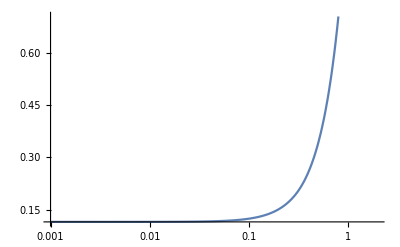

```mathematica
LogLinearPlot[Re[Interpolation[MqItersE[[1]]][p]]^2+ p^2, {p,10^-3,2}]
```

```mathematica
MqItersE[[1]]
```

{{1/100,0.3394078928530061596777710844-0.006845144743236697318641769026 ⅈ},{1/(10 √10),0.339308355376450825800751888827-0.0068029852867904587070641748332 ⅈ},{1/10,0.33806850178704089593657565071-0.00646489996481266346069154788 ⅈ},{1/(√10),0.321783848359174143772380285291-0.004412576928582671160116708233 ⅈ},{1,0.18032440185360941795675265896-0.00029337619371193355257595048365 ⅈ},{√10,-0.089695805776512204720286674783-0.000096296965722329911877886080907 ⅈ},{10,-0.26522442112357807600772444499-0.014128724321265925776995265131 ⅈ}}

```mathematica
Clear[ρ1Tmp,ρ2Tmp,ρ1DiscrTmp,ρ2DiscrTmp,PoleTmp ,ResidueTmp]
```

```mathematica
DumpSave["realtime_quark_specfuncs_tuesday1.mx",{
(*Diagrams*)
quarkSEVecIters,quarkSEVecItersE, quarkSEScalIters,quarkSEScalItersE,
	  (*Dressing functions*)
ZqIters, ZqItersE,
MqIters, MqItersE,
(*Poles & Residues*)
	  Poles, Residues,
	  (*Spectral functions*)
	 SpecFuncsρ1,SpecFuncsρ2
}]
```

{1}
 |  |  |  |

```mathematica
MqItersE
```

{{{1/100,-0.330436-0.00688734 ⅈ},{1/(10 10^(9/10)),-0.33043-0.00688434 ⅈ},{1/(10 10^(4/5)),-0.33042-0.00687972 ⅈ},{1/(10 10^(7/10)),-0.330404-0.0068726 ⅈ},{1/(10 10^(3/5)),-0.330377-0.00686163 ⅈ},{1/(10 √10),-0.330333-0.0068448 ⅈ},{1/(10 10^(2/5)),-0.330261-0.00681908 ⅈ},{1/(10 10^(3/10)),-0.330142-0.00678006 ⅈ},{1/(10 10^(1/5)),-0.329942-0.00672124 ⅈ},{1/(10 10^(1/10)),-0.32961-0.00663332 ⅈ},{1/10,-0.329052-0.00650317 ⅈ},{1/10^(9/10),-0.328117-0.0063128 ⅈ},{1/10^(4/5),-0.326547-0.00603863 ⅈ},{1/10^(7/10),-0.323914-0.00565187 ⅈ},{1/10^(3/5),-0.319512-0.00512181 ⅈ},{1/(√10),-0.312223-0.00442482 ⅈ},{1/10^(2/5),-0.300373-0.00356199 ⅈ},{1/10^(3/10),-0.281733-0.00258421 ⅈ},{1/10^(1/5),-0.253896-0.00160931 ⅈ},{1/10^(1/10),-0.215215-0.000799406 ⅈ},{1,-0.166027-0.00027916 ⅈ},{10^(1/10),-0.109195-0.00005166 ⅈ},{10^(1/5),-0.0492463-1.54162×10^-6 ⅈ},{10^(3/10),0.00941425-6.69809×10^-11 ⅈ},{10^(2/5),0.0638836-0.0000107093 ⅈ},{√10,0.113034-0.000125416 ⅈ},{10^(3/5),0.156986-0.000557426 ⅈ},{10^(7/10),0.19648-0.00165271 ⅈ},{10^(4/5),0.232185-0.00395485 ⅈ},{10^(9/10),0.264721-0.00833506 ⅈ},{10,0.294325-0.0162039 ⅈ},{10 10^(1/10),0.320582-0.0298016 ⅈ},{10 10^(1/5),0.341649-0.0524446 ⅈ},{10 10^(3/10),0.352502-0.0880741 ⅈ},{10 10^(2/5),0.342404-0.137954 ⅈ},{10 √10,0.296623-0.191544 ⅈ},{10 10^(3/5),0.214107-0.220721 ⅈ},{10 10^(7/10),0.125081-0.205323 ⅈ},{10 10^(4/5),0.061703-0.161013 ⅈ},{10 10^(9/10),0.0275706-0.114246 ⅈ},{100,0.0117449-0.0772293 ⅈ},{100 10^(1/10),0.00489815-0.051087 ⅈ},{100 10^(1/5),0.00202361-0.0334676 ⅈ},{100 10^(3/10),0.000832314-0.0218235 ⅈ},{100 10^(2/5),0.000341351-0.0141882 ⅈ},{100 √10,0.00013985-0.00921393 ⅈ},{100 10^(3/5),0.0000572325-0.0059767 ⅈ},{100 10^(7/10),0.0000234008-0.00387322 ⅈ},{100 10^(4/5),9.56038×10^-6-0.00250802 ⅈ},{100 10^(9/10),3.90311×10^-6-0.00162284 ⅈ},{1000,1.59243×10^-6-0.00104938 ⅈ}},{{1/100,0.366904-0.00834628 ⅈ},{1/(10 10^(9/10)),0.366897-0.00834276 ⅈ},{1/(10 10^(4/5)),0.366887-0.00833734 ⅈ},{1/(10 10^(7/10)),0.36687-0.00832897 ⅈ},{1/(10 10^(3/5)),0.366842-0.00831609 ⅈ},{1/(10 √10),0.366796-0.00829631 ⅈ},{1/(10 10^(2/5)),0.366721-0.00826608 ⅈ},{1/(10 10^(3/10)),0.366596-0.00822018 ⅈ},{1/(10 10^(1/5)),0.366388-0.00815095 ⅈ},{1/(10 10^(1/10)),0.36604-0.0080474 ⅈ},{1/10,0.365458-0.0078939 ⅈ},{1/10^(9/10),0.36448-0.00766926 ⅈ},{1/10^(4/5),0.362838-0.00734515 ⅈ},{1/10^(7/10),0.360084-0.00688706 ⅈ},{1/10^(3/5),0.355481-0.00625762 ⅈ},{1/(√10),0.347855-0.00542687 ⅈ},{1/10^(2/5),0.335456-0.00439356 ⅈ},{1/10^(3/10),0.315949-0.0032143 ⅈ},{1/10^(1/5),0.286809-0.00202637 ⅈ},{1/10^(1/10),0.246305-0.00102457 ⅈ},{1,0.194773-0.000366841 ⅈ},{10^(1/10),0.135187-0.0000699657 ⅈ},{10^(1/5),0.0722652-1.68816×10^-6 ⅈ},{10^(3/10),0.010616+1.15177×10^-10 ⅈ},{10^(2/5),-0.0466984-0.0000111214 ⅈ},{√10,-0.0984607-0.000155533 ⅈ},{10^(3/5),-0.144737-0.000742262 ⅈ},{10^(7/10),-0.18627-0.00230027 ⅈ},{10^(4/5),-0.223688-0.00567746 ⅈ},{10^(9/10),-0.257489-0.0122322 ⅈ},{10,-0.287515-0.02412 ⅈ},{10 10^(1/10),-0.312261-0.0445723 ⅈ},{10 10^(1/5),-0.327227-0.0775747 ⅈ},{10 10^(3/10),-0.322346-0.124914 ⅈ},{10 10^(2/5),-0.283021-0.177401 ⅈ},{10 √10,-0.206673-0.208089 ⅈ},{10 10^(3/5),-0.121625-0.195795 ⅈ},{10 10^(7/10),-0.0601504-0.154359 ⅈ},{10 10^(4/5),-0.026869-0.109693 ⅈ},{10 10^(9/10),-0.0114286-0.0741272 ⅈ},{100,-0.0047569-0.0489774 ⅈ},{100 10^(1/10),-0.00196108-0.0320338 ⅈ},{100 10^(1/5),-0.000804839-0.02085 ⅈ},{100 10^(3/10),-0.000329517-0.013535 ⅈ},{100 10^(2/5),-0.000134847-0.0087741 ⅈ},{100 √10,-0.0000549817-0.00567528 ⅈ},{100 10^(3/5),-0.000022433-0.00367031 ⅈ},{100 10^(7/10),-9.14611×10^-6-0.00237182 ⅈ},{100 10^(4/5),-3.72651×10^-6-0.00153168 ⅈ},{100 10^(9/10),-1.51744×10^-6-0.000988525 ⅈ},{1000,-6.17569×10^-7-0.000637631 ⅈ}},{{1/100,0.370119-0.00815836 ⅈ},{1/(10 10^(9/10)),0.370112-0.00815481 ⅈ},{1/(10 10^(4/5)),0.370102-0.00814936 ⅈ},{1/(10 10^(7/10)),0.370085-0.00814094 ⅈ},{1/(10 10^(3/5)),0.370057-0.00812798 ⅈ},{1/(10 √10),0.370011-0.0081081 ⅈ},{1/(10 10^(2/5)),0.369934-0.00807773 ⅈ},{1/(10 10^(3/10)),0.369808-0.00803165 ⅈ},{1/(10 10^(1/5)),0.369598-0.00796223 ⅈ},{1/(10 10^(1/10)),0.369246-0.0078585 ⅈ},{1/10,0.368658-0.00770501 ⅈ},{1/10^(9/10),0.36767-0.0074806 ⅈ},{1/10^(4/5),0.366011-0.00715756 ⅈ},{1/10^(7/10),0.363227-0.00670209 ⅈ},{1/10^(3/5),0.358574-0.00607813 ⅈ},{1/(√10),0.350866-0.0052578 ⅈ},{1/10^(2/5),0.338334-0.00424201 ⅈ},{1/10^(3/10),0.318618-0.00308952 ⅈ},{1/10^(1/5),0.289171-0.00193713 ⅈ},{1/10^(1/10),0.248252-0.000974053 ⅈ},{1,0.196216-0.000348089 ⅈ},{10^(1/10),0.136093-0.0000676873 ⅈ},{10^(1/5),0.072674-2.31955×10^-6 ⅈ},{10^(3/10),0.0106196+8.19818×10^-11 ⅈ},{10^(2/5),-0.0469995-8.46605×10^-6 ⅈ},{√10,-0.0989935-0.000117938 ⅈ},{10^(3/5),-0.145499-0.000555471 ⅈ},{10^(7/10),-0.187315-0.00169786 ⅈ},{10^(4/5),-0.225172-0.00414419 ⅈ},{10^(9/10),-0.259743-0.00886227 ⅈ},{10,-0.291261-0.017425 ⅈ},{10 10^(1/10),-0.319177-0.0323249 ⅈ},{10 10^(1/5),-0.341204-0.0571866 ⅈ},{10 10^(3/10),-0.351287-0.0960046 ⅈ},{10 10^(2/5),-0.337141-0.148788 ⅈ},{10 √10,-0.284214-0.201252 ⅈ},{10 10^(3/5),-0.197096-0.222982 ⅈ},{10 10^(7/10),-0.110805-0.199727 ⅈ},{10 10^(4/5),-0.0532883-0.152757 ⅈ},{10 10^(9/10),-0.0234931-0.106973 ⅈ},{100,-0.00994098-0.0718438 ⅈ},{100 10^(1/10),-0.00413048-0.0473547 ⅈ},{100 10^(1/5),-0.00170215-0.0309471 ⅈ},{100 10^(3/10),-0.000698645-0.0201393 ⅈ},{100 10^(2/5),-0.000285978-0.0130685 ⅈ},{100 √10,-0.00011695-0.00847153 ⅈ},{100 10^(3/5),-0.0000477765-0.00548553 ⅈ},{100 10^(7/10),-0.0000195006-0.00354878 ⅈ},{100 10^(4/5),-7.95332×10^-6-0.00229402 ⅈ},{100 10^(9/10),-3.24178×10^-6-0.00148198 ⅈ},{1000,-1.32054×10^-6-0.000956793 ⅈ}},{{1/100,-0.330436-0.00688734 ⅈ},{1/(10 10^(9/10)),-0.33043-0.00688434 ⅈ},{1/(10 10^(4/5)),-0.33042-0.00687972 ⅈ},{1/(10 10^(7/10)),-0.330404-0.0068726 ⅈ},{1/(10 10^(3/5)),-0.330377-0.00686163 ⅈ},{1/(10 √10),-0.330333-0.0068448 ⅈ},{1/(10 10^(2/5)),-0.330261-0.00681908 ⅈ},{1/(10 10^(3/10)),-0.330142-0.00678006 ⅈ},{1/(10 10^(1/5)),-0.329942-0.00672124 ⅈ},{1/(10 10^(1/10)),-0.32961-0.00663332 ⅈ},{1/10,-0.329052-0.00650317 ⅈ},{1/10^(9/10),-0.328117-0.0063128 ⅈ},{1/10^(4/5),-0.326547-0.00603863 ⅈ},{1/10^(7/10),-0.323914-0.00565187 ⅈ},{1/10^(3/5),-0.319512-0.00512181 ⅈ},{1/(√10),-0.312223-0.00442482 ⅈ},{1/10^(2/5),-0.300373-0.00356199 ⅈ},{1/10^(3/10),-0.281733-0.00258421 ⅈ},{1/10^(1/5),-0.253896-0.00160931 ⅈ},{1/10^(1/10),-0.215215-0.000799406 ⅈ},{1,-0.166027-0.00027916 ⅈ},{10^(1/10),-0.109195-0.00005166 ⅈ},{10^(1/5),-0.0492463-1.54162×10^-6 ⅈ},{10^(3/10),0.00941425-6.69809×10^-11 ⅈ},{10^(2/5),0.0638836-0.0000107093 ⅈ},{√10,0.113034-0.000125416 ⅈ},{10^(3/5),0.156986-0.000557426 ⅈ},{10^(7/10),0.19648-0.00165271 ⅈ},{10^(4/5),0.232185-0.00395485 ⅈ},{10^(9/10),0.264721-0.00833506 ⅈ},{10,0.294325-0.0162039 ⅈ},{10 10^(1/10),0.320582-0.0298016 ⅈ},{10 10^(1/5),0.341649-0.0524446 ⅈ},{10 10^(3/10),0.352502-0.0880741 ⅈ},{10 10^(2/5),0.342404-0.137954 ⅈ},{10 √10,0.296623-0.191544 ⅈ},{10 10^(3/5),0.214107-0.220721 ⅈ},{10 10^(7/10),0.125081-0.205323 ⅈ},{10 10^(4/5),0.061703-0.161013 ⅈ},{10 10^(9/10),0.0275706-0.114246 ⅈ},{100,0.0117449-0.0772293 ⅈ},{100 10^(1/10),0.00489815-0.051087 ⅈ},{100 10^(1/5),0.00202361-0.0334676 ⅈ},{100 10^(3/10),0.000832314-0.0218235 ⅈ},{100 10^(2/5),0.000341351-0.0141882 ⅈ},{100 √10,0.00013985-0.00921393 ⅈ},{100 10^(3/5),0.0000572325-0.0059767 ⅈ},{100 10^(7/10),0.0000234008-0.00387322 ⅈ},{100 10^(4/5),9.56038×10^-6-0.00250802 ⅈ},{100 10^(9/10),3.90311×10^-6-0.00162284 ⅈ},{1000,1.59243×10^-6-0.00104938 ⅈ}}}

### Consistency checks + Plots

Check if respective parts of the Euclidean quark propagator (curlyA and curlyB) coincide with the propagator extracted from the spectral representation.

```mathematica
quarkPropA = Table[{p,NIntegrate[λ/π*Interpolation[SpecFuncsρ1[[1]]][λ]/(p^2+λ^2),{λ,10^-3,10}]},{p,10^Range[-3,1,1/10]}];
```

```mathematica
Interpolation[quarkPropA]
```

InterpolatingFunction[…]

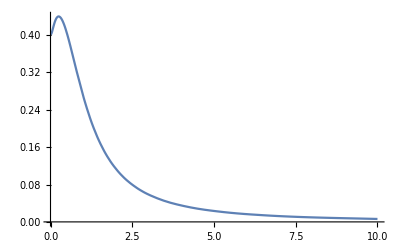

```mathematica
Plot[%2451[x]/10,{x,0.001,10.}]
```

InterpolatingFunction::dmval: Input value {0.00100019} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00120702} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00145662} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

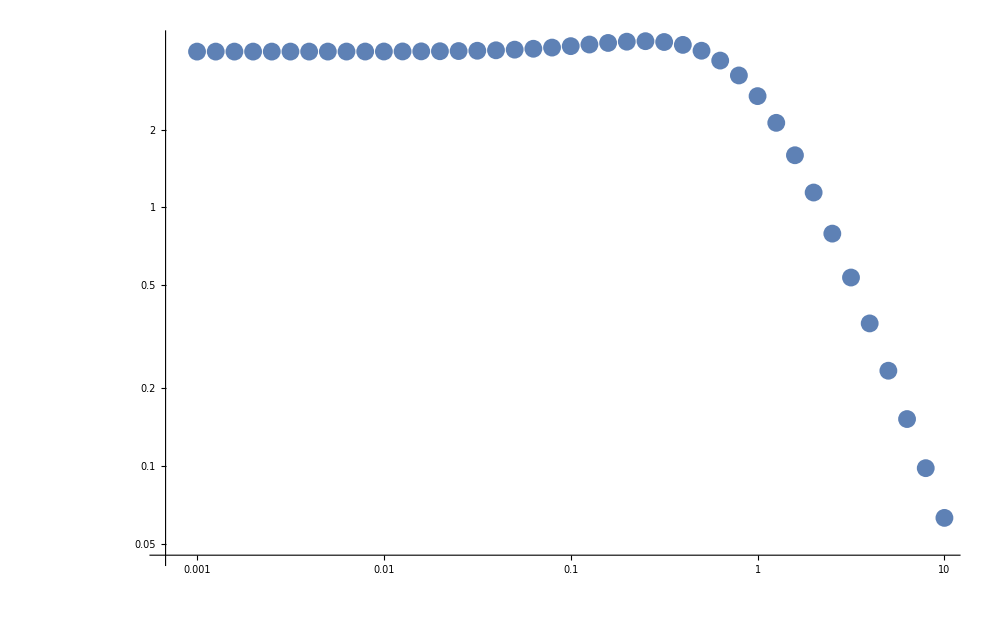

```mathematica
With[{i=1},Show[ListLogLogPlot[quarkPropA],LogLogPlot[(Interpolation[ZqItersE[[1]]][p]/(p^2 + Interpolation[MqItersE[[1]]]^2[p])),{p,10^-3,10}],ImageSize->1000]]
```

Finally plot the result for the spectral functions :

```mathematica
With[{i=1},Plot[Interpolation[SpecFuncsρ1[[i]]],{λ,10^-3,10^0},ImageSize->800]]
```

-Graphics-

```mathematica
<<realtime_quark_specfuncs_monday1.mx;
```

```mathematica
MqItersE
```

{{{1/100,-0.330436-0.00688734 ⅈ},{1/(10 10^(9/10)),-0.33043-0.00688434 ⅈ},{1/(10 10^(4/5)),-0.33042-0.00687972 ⅈ},{1/(10 10^(7/10)),-0.330404-0.0068726 ⅈ},{1/(10 10^(3/5)),-0.330377-0.00686163 ⅈ},{1/(10 √10),-0.330333-0.0068448 ⅈ},{1/(10 10^(2/5)),-0.330261-0.00681908 ⅈ},{1/(10 10^(3/10)),-0.330142-0.00678006 ⅈ},{1/(10 10^(1/5)),-0.329942-0.00672124 ⅈ},{1/(10 10^(1/10)),-0.32961-0.00663332 ⅈ},{1/10,-0.329052-0.00650317 ⅈ},{1/10^(9/10),-0.328117-0.0063128 ⅈ},{1/10^(4/5),-0.326547-0.00603863 ⅈ},{1/10^(7/10),-0.323914-0.00565187 ⅈ},{1/10^(3/5),-0.319512-0.00512181 ⅈ},{1/(√10),-0.312223-0.00442482 ⅈ},{1/10^(2/5),-0.300373-0.00356199 ⅈ},{1/10^(3/10),-0.281733-0.00258421 ⅈ},{1/10^(1/5),-0.253896-0.00160931 ⅈ},{1/10^(1/10),-0.215215-0.000799406 ⅈ},{1,-0.166027-0.00027916 ⅈ},{10^(1/10),-0.109195-0.00005166 ⅈ},{10^(1/5),-0.0492463-1.54162×10^-6 ⅈ},{10^(3/10),0.00941425-6.69809×10^-11 ⅈ},{10^(2/5),0.0638836-0.0000107093 ⅈ},{√10,0.113034-0.000125416 ⅈ},{10^(3/5),0.156986-0.000557426 ⅈ},{10^(7/10),0.19648-0.00165271 ⅈ},{10^(4/5),0.232185-0.00395485 ⅈ},{10^(9/10),0.264721-0.00833506 ⅈ},{10,0.294325-0.0162039 ⅈ},{10 10^(1/10),0.320582-0.0298016 ⅈ},{10 10^(1/5),0.341649-0.0524446 ⅈ},{10 10^(3/10),0.352502-0.0880741 ⅈ},{10 10^(2/5),0.342404-0.137954 ⅈ},{10 √10,0.296623-0.191544 ⅈ},{10 10^(3/5),0.214107-0.220721 ⅈ},{10 10^(7/10),0.125081-0.205323 ⅈ},{10 10^(4/5),0.061703-0.161013 ⅈ},{10 10^(9/10),0.0275706-0.114246 ⅈ},{100,0.0117449-0.0772293 ⅈ},{100 10^(1/10),0.00489815-0.051087 ⅈ},{100 10^(1/5),0.00202361-0.0334676 ⅈ},{100 10^(3/10),0.000832314-0.0218235 ⅈ},{100 10^(2/5),0.000341351-0.0141882 ⅈ},{100 √10,0.00013985-0.00921393 ⅈ},{100 10^(3/5),0.0000572325-0.0059767 ⅈ},{100 10^(7/10),0.0000234008-0.00387322 ⅈ},{100 10^(4/5),9.56038×10^-6-0.00250802 ⅈ},{100 10^(9/10),3.90311×10^-6-0.00162284 ⅈ},{1000,1.59243×10^-6-0.00104938 ⅈ}},{{1/100,0.366904-0.00834628 ⅈ},{1/(10 10^(9/10)),0.366897-0.00834276 ⅈ},{1/(10 10^(4/5)),0.366887-0.00833734 ⅈ},{1/(10 10^(7/10)),0.36687-0.00832897 ⅈ},{1/(10 10^(3/5)),0.366842-0.00831609 ⅈ},{1/(10 √10),0.366796-0.00829631 ⅈ},{1/(10 10^(2/5)),0.366721-0.00826608 ⅈ},{1/(10 10^(3/10)),0.366596-0.00822018 ⅈ},{1/(10 10^(1/5)),0.366388-0.00815095 ⅈ},{1/(10 10^(1/10)),0.36604-0.0080474 ⅈ},{1/10,0.365458-0.0078939 ⅈ},{1/10^(9/10),0.36448-0.00766926 ⅈ},{1/10^(4/5),0.362838-0.00734515 ⅈ},{1/10^(7/10),0.360084-0.00688706 ⅈ},{1/10^(3/5),0.355481-0.00625762 ⅈ},{1/(√10),0.347855-0.00542687 ⅈ},{1/10^(2/5),0.335456-0.00439356 ⅈ},{1/10^(3/10),0.315949-0.0032143 ⅈ},{1/10^(1/5),0.286809-0.00202637 ⅈ},{1/10^(1/10),0.246305-0.00102457 ⅈ},{1,0.194773-0.000366841 ⅈ},{10^(1/10),0.135187-0.0000699657 ⅈ},{10^(1/5),0.0722652-1.68816×10^-6 ⅈ},{10^(3/10),0.010616+1.15177×10^-10 ⅈ},{10^(2/5),-0.0466984-0.0000111214 ⅈ},{√10,-0.0984607-0.000155533 ⅈ},{10^(3/5),-0.144737-0.000742262 ⅈ},{10^(7/10),-0.18627-0.00230027 ⅈ},{10^(4/5),-0.223688-0.00567746 ⅈ},{10^(9/10),-0.257489-0.0122322 ⅈ},{10,-0.287515-0.02412 ⅈ},{10 10^(1/10),-0.312261-0.0445723 ⅈ},{10 10^(1/5),-0.327227-0.0775747 ⅈ},{10 10^(3/10),-0.322346-0.124914 ⅈ},{10 10^(2/5),-0.283021-0.177401 ⅈ},{10 √10,-0.206673-0.208089 ⅈ},{10 10^(3/5),-0.121625-0.195795 ⅈ},{10 10^(7/10),-0.0601504-0.154359 ⅈ},{10 10^(4/5),-0.026869-0.109693 ⅈ},{10 10^(9/10),-0.0114286-0.0741272 ⅈ},{100,-0.0047569-0.0489774 ⅈ},{100 10^(1/10),-0.00196108-0.0320338 ⅈ},{100 10^(1/5),-0.000804839-0.02085 ⅈ},{100 10^(3/10),-0.000329517-0.013535 ⅈ},{100 10^(2/5),-0.000134847-0.0087741 ⅈ},{100 √10,-0.0000549817-0.00567528 ⅈ},{100 10^(3/5),-0.000022433-0.00367031 ⅈ},{100 10^(7/10),-9.14611×10^-6-0.00237182 ⅈ},{100 10^(4/5),-3.72651×10^-6-0.00153168 ⅈ},{100 10^(9/10),-1.51744×10^-6-0.000988525 ⅈ},{1000,-6.17569×10^-7-0.000637631 ⅈ}},{{1/100,0.370119-0.00815836 ⅈ},{1/(10 10^(9/10)),0.370112-0.00815481 ⅈ},{1/(10 10^(4/5)),0.370102-0.00814936 ⅈ},{1/(10 10^(7/10)),0.370085-0.00814094 ⅈ},{1/(10 10^(3/5)),0.370057-0.00812798 ⅈ},{1/(10 √10),0.370011-0.0081081 ⅈ},{1/(10 10^(2/5)),0.369934-0.00807773 ⅈ},{1/(10 10^(3/10)),0.369808-0.00803165 ⅈ},{1/(10 10^(1/5)),0.369598-0.00796223 ⅈ},{1/(10 10^(1/10)),0.369246-0.0078585 ⅈ},{1/10,0.368658-0.00770501 ⅈ},{1/10^(9/10),0.36767-0.0074806 ⅈ},{1/10^(4/5),0.366011-0.00715756 ⅈ},{1/10^(7/10),0.363227-0.00670209 ⅈ},{1/10^(3/5),0.358574-0.00607813 ⅈ},{1/(√10),0.350866-0.0052578 ⅈ},{1/10^(2/5),0.338334-0.00424201 ⅈ},{1/10^(3/10),0.318618-0.00308952 ⅈ},{1/10^(1/5),0.289171-0.00193713 ⅈ},{1/10^(1/10),0.248252-0.000974053 ⅈ},{1,0.196216-0.000348089 ⅈ},{10^(1/10),0.136093-0.0000676873 ⅈ},{10^(1/5),0.072674-2.31955×10^-6 ⅈ},{10^(3/10),0.0106196+8.19818×10^-11 ⅈ},{10^(2/5),-0.0469995-8.46605×10^-6 ⅈ},{√10,-0.0989935-0.000117938 ⅈ},{10^(3/5),-0.145499-0.000555471 ⅈ},{10^(7/10),-0.187315-0.00169786 ⅈ},{10^(4/5),-0.225172-0.00414419 ⅈ},{10^(9/10),-0.259743-0.00886227 ⅈ},{10,-0.291261-0.017425 ⅈ},{10 10^(1/10),-0.319177-0.0323249 ⅈ},{10 10^(1/5),-0.341204-0.0571866 ⅈ},{10 10^(3/10),-0.351287-0.0960046 ⅈ},{10 10^(2/5),-0.337141-0.148788 ⅈ},{10 √10,-0.284214-0.201252 ⅈ},{10 10^(3/5),-0.197096-0.222982 ⅈ},{10 10^(7/10),-0.110805-0.199727 ⅈ},{10 10^(4/5),-0.0532883-0.152757 ⅈ},{10 10^(9/10),-0.0234931-0.106973 ⅈ},{100,-0.00994098-0.0718438 ⅈ},{100 10^(1/10),-0.00413048-0.0473547 ⅈ},{100 10^(1/5),-0.00170215-0.0309471 ⅈ},{100 10^(3/10),-0.000698645-0.0201393 ⅈ},{100 10^(2/5),-0.000285978-0.0130685 ⅈ},{100 √10,-0.00011695-0.00847153 ⅈ},{100 10^(3/5),-0.0000477765-0.00548553 ⅈ},{100 10^(7/10),-0.0000195006-0.00354878 ⅈ},{100 10^(4/5),-7.95332×10^-6-0.00229402 ⅈ},{100 10^(9/10),-3.24178×10^-6-0.00148198 ⅈ},{1000,-1.32054×10^-6-0.000956793 ⅈ}}}

```mathematica
Interpolation[SpecFuncsρ1[[3]]]
```

InterpolatingFunction[…]

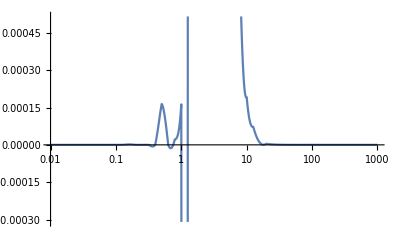

```mathematica
LogLinearPlot[%1370[x],{x,0.01,1000.}]
```

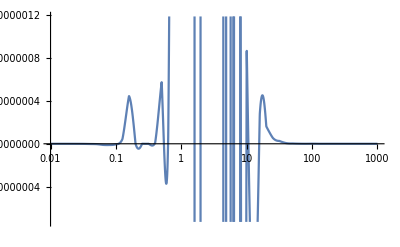

```mathematica
LogLinearPlot[%570[x],{x,0.01,1000.}]
```

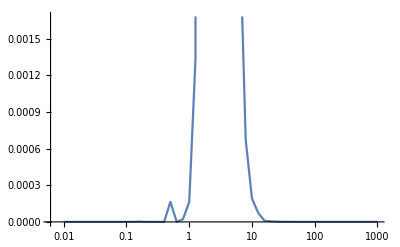

```mathematica
ListLogLinearPlot[SpecFuncsρ1[[3]], Joined-> True]
```

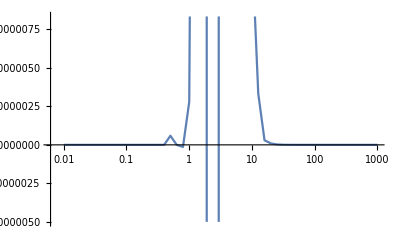

```mathematica
ListLogLinearPlot[SpecFuncsρ2[[3]], Joined-> True]
```

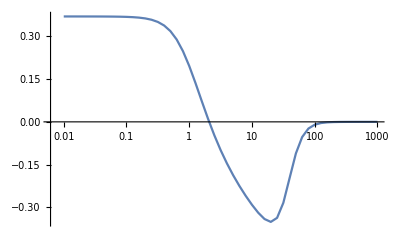

```mathematica
ListLogLinearPlot[Re[MqItersE[[3]]], Joined-> True]
```

## Iteration 2 ("ρ2 = 0") -- Not yet included

```mathematica
<<"realtime_quark_specfuncs_first_trials.mx"
```

```mathematica
Interpolation[ZqItersE[[1]]]
```

InterpolatingFunction[…]

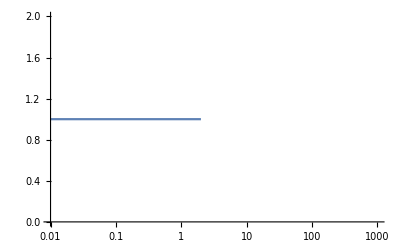

```mathematica
LogLinearPlot[%1149[x],{x,0.01,1000.}]
```

## Plots for the Main Part of the thesis (Results)

```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
```

LinTicks::shdw: Symbol LinTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

LogTicks::shdw: Symbol LogTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

ShowTickLabels::shdw: Symbol ShowTickLabels appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

ShowMinorTicks::shdw: Symbol ShowMinorTicks appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

TickLabelStep::shdw: Symbol TickLabelStep appears in multiple contexts {CustomTicks`,Global`}; definitions in context CustomTicks` may shadow or be shadowed by other definitions.

```mathematica
exportPath=FileNameJoin[{NotebookDirectory[],"plots"}]; (*specify where plots are saved*)
```

```mathematica
SetAttributes[exportFigure,HoldFirst]
exportFigure[figure_]:=Export[FileNameJoin[{exportPath,StringJoin[ToString[SymbolName[Unevaluated@figure]],".pdf"]}],figure]; (*Plots should be safed as PDF*)
```

```mathematica
SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}];
SetOptions[LogTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}];
```

```mathematica
(*Some quick plot settings*)
MScRed = RGBColor[157/255,0,0]
MScBlue = RGBColor[1/255,1/255,141/255]
MScGreen = RGBColor[0,119/255,85/255]
MScGray = RGBColor[102/255, 102/255, 142/255]

MScColors = {MScBlue,MScRed, MScGreen}

MScFont = {FontFamily->"Palatino",FontSize->40}

SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}];
SetOptions[LogTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}];
```

RGBColor[Rational[157, 255], 0, 0]

RGBColor[Rational[1, 255], Rational[1, 255], Rational[47, 85]]

RGBColor[0, Rational[7, 15], Rational[1, 3]]

RGBColor[Rational[2, 5], Rational[2, 5], Rational[142, 255]]

{RGBColor[Rational[1, 255], Rational[1, 255], Rational[47, 85]],RGBColor[Rational[157, 255], 0, 0],RGBColor[0, Rational[7, 15], Rational[1, 3]]}

{FontFamily→Palatino,FontSize→40}

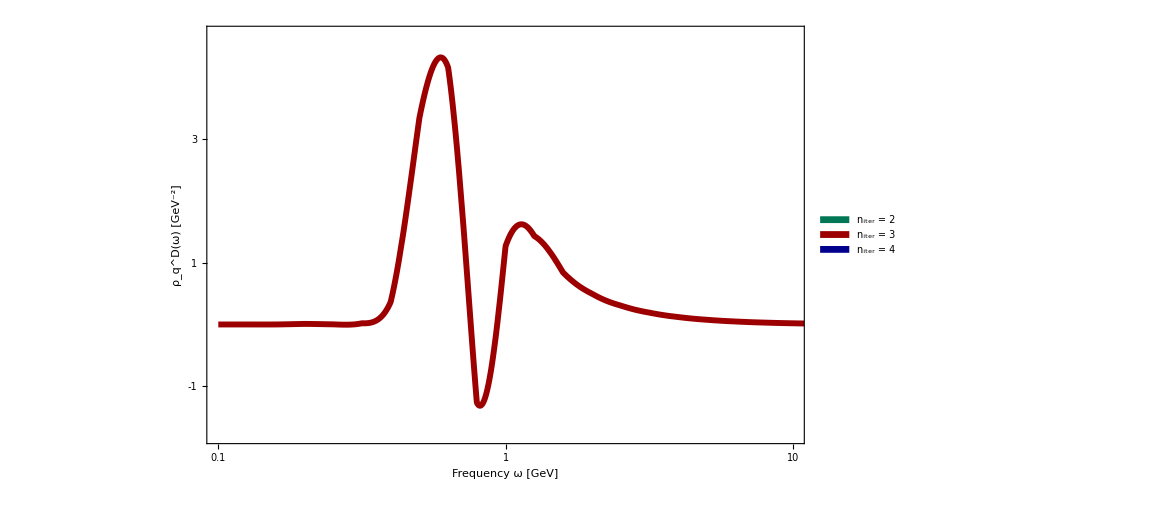

```mathematica
rhoqDPlot = LogLinearPlot[{(*Interpolation[SpecFuncsρ1[[2]]][ω],Interpolation[SpecFuncsρ1[[3]]][ω]*)(*, Interpolation[SpecFuncsρ1[[4]]][ω],*) , Interpolation[SpecFuncsρ1[[1]]][ω]},{ω,10^-1,10^2},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-1,10^1},yRange={-1.8, 4.7}},
PlotStyle->{Directive[MScGreen,Thickness[0.005]],Directive[MScRed,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Frequency ω [GeV]", "  ρ_q^D(ω) [GeV^-2]"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->True,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->True]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{MScGreen, MScRed, MScBlue},{"n_iter = 2", "n_iter = 3", "n_iter = 4"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.7,.93}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[rhoqDPlot];
```

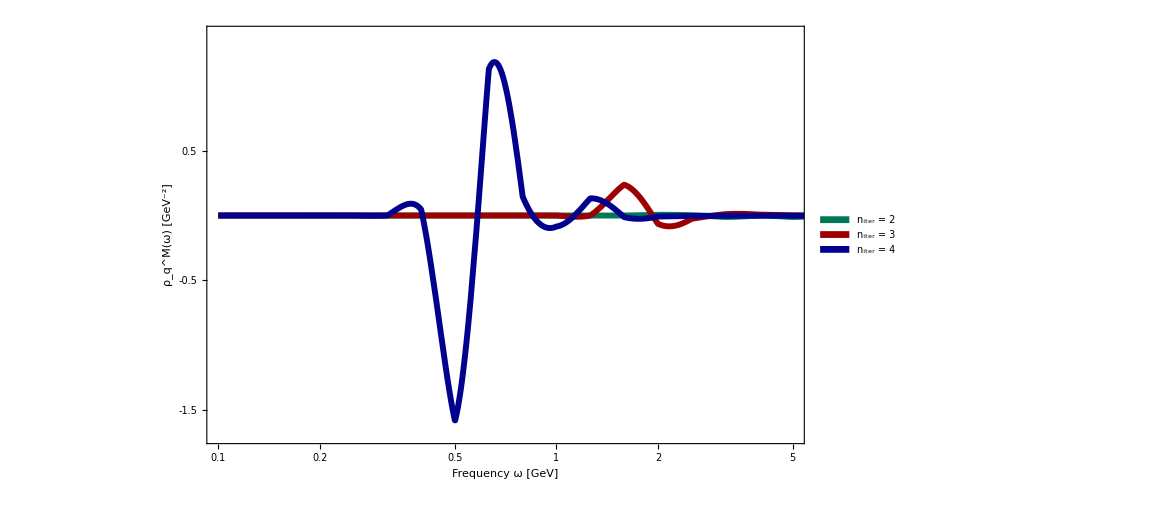

```mathematica
rhoqMPlot=LogLinearPlot[{Interpolation[SpecFuncsρ2[[2]]][ω],Interpolation[SpecFuncsρ2[[3]]][ω], Interpolation[SpecFuncsρ2[[4]]][ω]},{ω,10^-1,10^2},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-1,0.5*10^1},yRange={-1.7,1.4}},
PlotStyle->{Directive[MScGreen,Thickness[0.005]],Directive[MScRed,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Frequency ω [GeV]", "  ρ_q^M(ω) [GeV^-2]"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->True,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->True]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{MScGreen,MScRed, MScBlue},{"n_iter = 2", "n_iter = 3", "n_iter = 4"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.7,.45}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[rhoqMPlot];
```

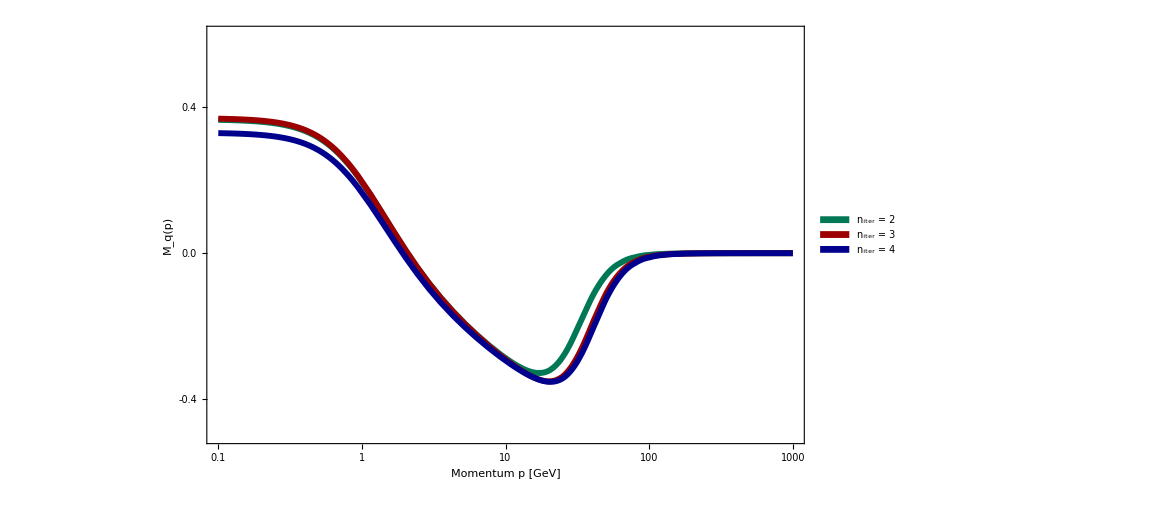

```mathematica
MqPlot = LogLinearPlot[{Interpolation[Re[MqItersE[[2]]]][p],Interpolation[Re[MqItersE[[3]]]][p], -Interpolation[Re[MqItersE[[4]]]][p]},{p,10^-1,10^3},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-1,10^3},yRange={-0.5,0.6}},
PlotStyle->{Directive[MScGreen,Thickness[0.005]],Directive[MScRed,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum p [GeV]", "M_q(p)"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{MScGreen,MScRed, MScBlue},{"n_iter = 2", "n_iter = 3", "n_iter = 4"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.7,.93}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[MqPlot];
```

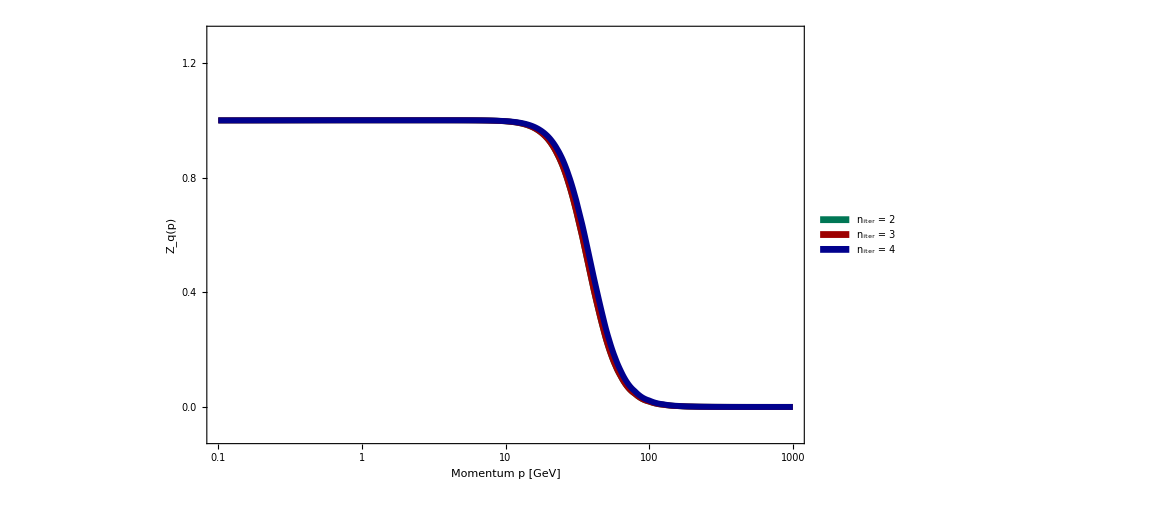

```mathematica
ZqPlot = LogLinearPlot[{Interpolation[Re[ZqItersE[[3]]]][p],Interpolation[Re[ZqItersE[[3]]]][p], Interpolation[Re[ZqItersE[[4]]]][p]},{p,10^-1,10^3},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-1,10^3},yRange={-0.1,1.3}},
PlotStyle->{Directive[MScGreen,Thickness[0.005]],Directive[MScRed,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum p [GeV]", "  Z_q(p) "},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{MScGreen,MScRed, MScBlue},{"n_iter = 2", "n_iter = 3", "n_iter = 4"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.7,.93}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
exportFigure[ZqPlot];
```

#### Comparison with Euclidean Propagator

```mathematica
DiracVector = Table[{p,NIntegrate[λ/π*Interpolation[SpecFuncsρ1[[3]]][λ]/(p^2+λ^2),{λ,10^-3,10^2}]},{p,10^Range[-3,2,1/10]}];
```

InterpolatingFunction::dmval: Input value {0.00100019} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

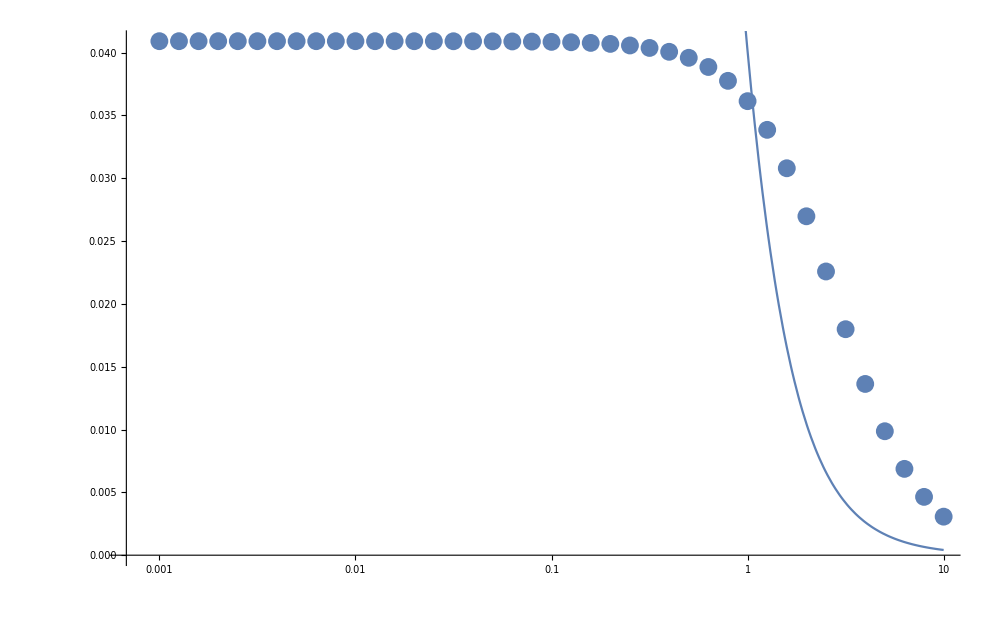

```mathematica
Show[ListLogLinearPlot[DiracVector], LogLinearPlot[Interpolation[Re[ZqItersE[[3]]]][p]/(p^2+Interpolation[Re[MqItersE[[3]]]][p]^2)/24, {p,10^-3,10}],ImageSize->1000]
```

```mathematica
Interpolation[ZqItersE[[3]]]/(p^2+Interpolation[MqItersE[[3]]]^2)
```

InterpolatingFunction[…]/(p^2+InterpolatingFunction[…]^2)

```mathematica
DiracScalar = Table[{p,NIntegrate[λ/π*Interpolation[SpecFuncsρ2[[3]]][λ]/(p^2+λ^2),{λ,10^-3,10^2}]},{p,10^Range[-3,2,1/10]}];
```

InterpolatingFunction::dmval: Input value {0.00100019} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

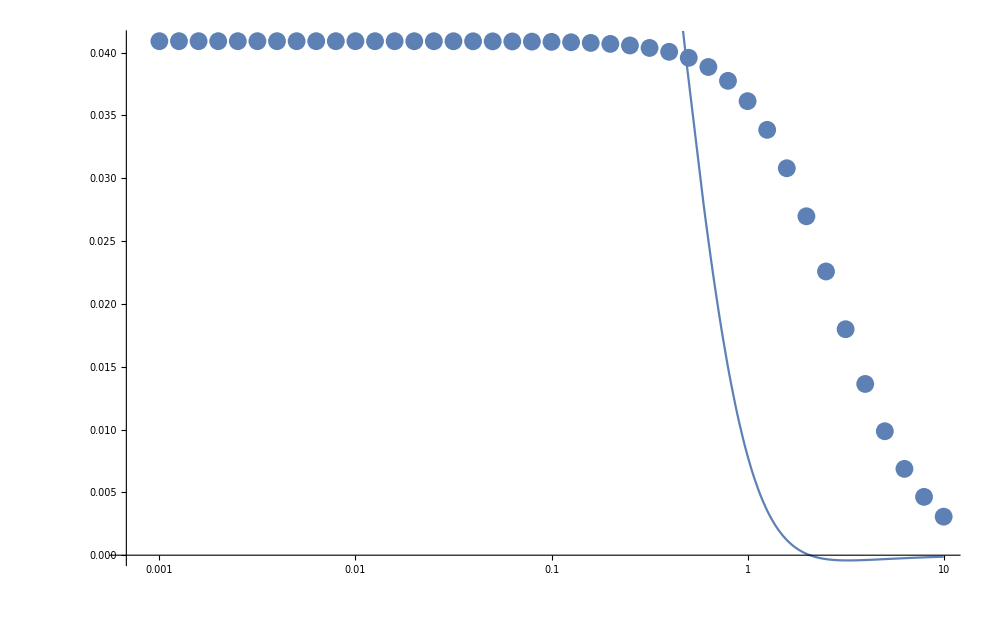

```mathematica
Show[ListLogLinearPlot[DiracVector], LogLinearPlot[(Interpolation[Re[MqItersE[[3]]]][p])/(p^2+Interpolation[Re[MqItersE[[3]]]][p]^2)/24, {p,10^-3,10}],ImageSize->1000]
```

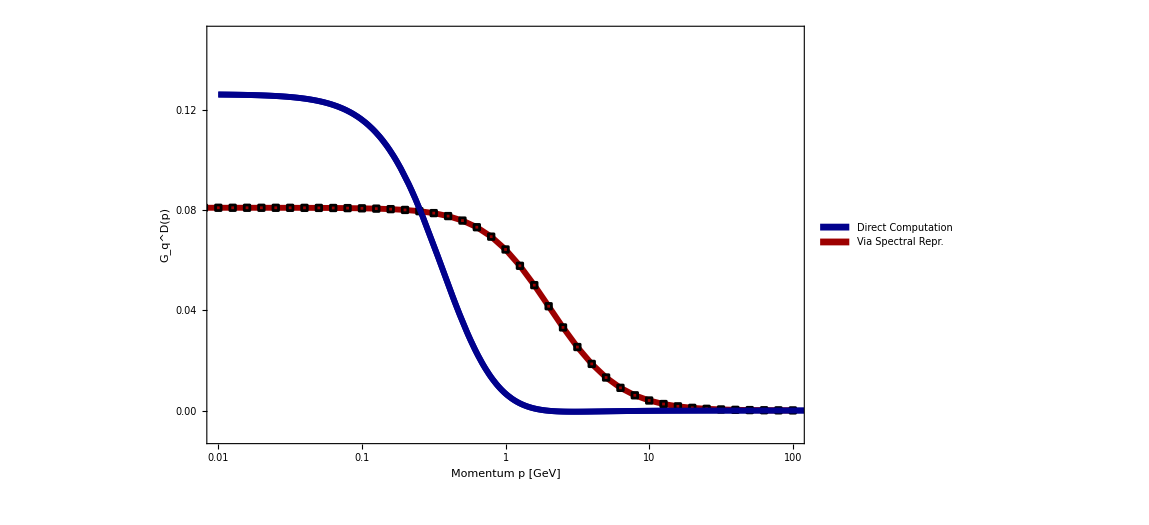

```mathematica
BenchmarkPlotVec= Show[{
LogLinearPlot[(-Interpolation[Re[MqItersE[[4]]]][p])/(p^2+Interpolation[Re[MqItersE[[4]]]][p]^2)/24, {p,10^-2,10^3},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-2,10^2},yRange={-0.01,0.15}},
PlotStyle->{ Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum p [GeV]", "  G_q^D(p) "},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{ MScBlue, MScRed},{ "Direct Computation", "Via Spectral Repr."}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",30}],
{Scaled[{0.5,.93}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
],
 ListLogLinearPlot[DiracVector, Joined-> True,
PlotMarkers->Evaluate[{Graphics[{EdgeForm[{Black,Thickness[.1]}],Polygon[CirclePoints[4]]}],0.03}&/@{Black}],
PlotStyle->Evaluate[Directive[MScRed,Thickness[0.005]]]],
LogLinearPlot[(-Interpolation[Re[MqItersE[[4]]]][p])/(p^2+Interpolation[Re[MqItersE[[4]]]][p]^2)/24, {p,10^-2,10^3},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-2,10^2},yRange={-0.01,0.15}},
PlotStyle->{ Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum p [GeV]", "  G_q^D(p) "},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}}(*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
 }]
exportFigure[BenchmarkPlotVec];
```

```mathematica
Re[ZqItersE[[3]]]
```

{{1/100,0.999514},{1/(10 10^(9/10)),0.999515},{1/(10 10^(4/5)),0.999515},{1/(10 10^(7/10)),0.999516},{1/(10 10^(3/5)),0.999518},{1/(10 √10),0.99952},{1/(10 10^(2/5)),0.999523},{1/(10 10^(3/10)),0.999529},{1/(10 10^(1/5)),0.999536},{1/(10 10^(1/10)),0.999547},{1/10,0.999563},{1/10^(9/10),0.999586},{1/10^(4/5),0.999618},{1/10^(7/10),0.99966},{1/10^(3/5),0.999713},{1/(√10),0.999775},{1/10^(2/5),0.999843},{1/10^(3/10),0.999906},{1/10^(1/5),0.999955},{1/10^(1/10),0.999985},{1,0.999997},{10^(1/10),1.},{10^(1/5),1.},{10^(3/10),1.},{10^(2/5),1.},{√10,0.999999},{10^(3/5),0.999985},{10^(7/10),0.999918},{10^(4/5),0.999661},{10^(9/10),0.998837},{10,0.996434},{10 10^(1/10),0.989847},{10 10^(1/5),0.972677},{10 10^(3/10),0.930501},{10 10^(2/5),0.836985},{10 √10,0.666042},{10 10^(3/5),0.43861},{10 10^(7/10),0.235346},{10 10^(4/5),0.10849},{10 10^(9/10),0.0460121},{100,0.0187864},{100 10^(1/10),0.0075506},{100 10^(1/5),0.00301609},{100 10^(3/10),0.00120199},{100 10^(2/5),0.000478635},{100 √10,0.000190544},{100 10^(3/5),0.0000758506},{100 10^(7/10),0.0000301943},{100 10^(4/5),0.0000120198},{100 10^(9/10),4.78497×10^-6},{1000,1.90488×10^-6}}

InterpolatingFunction::dmval: Input value {0.0100024} lies outside the range of data in the interpolating function. Extrapolation will be used.

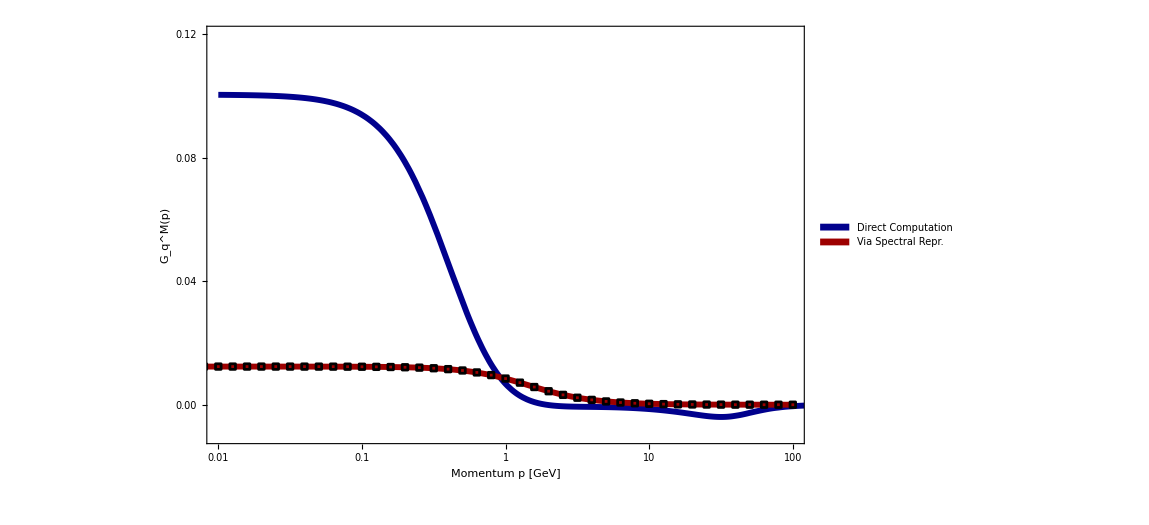

```mathematica
BenchmarkPlotScal= Show[{
LogLinearPlot[(Interpolation[-Re[ZqItersE[[4]]]][p]*Interpolation[Re[MqItersE[[4]]]][p])/(p^2+Interpolation[Re[MqItersE[[3]]]][p]^2)/24, {p,10^-2,10^3},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-2,10^2},yRange={-0.01,0.12}},
PlotStyle->{ Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Momentum p [GeV]", "  G_q^M(p) "},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{ MScBlue, MScRed},{ "Direct Computation", "Via Spectral Repr."}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",30}],
{Scaled[{0.5,.93}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
], ListLogLinearPlot[DiracScalar, Joined-> True,
PlotMarkers->Evaluate[{Graphics[{EdgeForm[{Black,Thickness[.1]}],Polygon[CirclePoints[4]]}],0.03}&/@{Black}],
PlotStyle->Evaluate[Directive[MScRed,Thickness[0.005]]]] }]
exportFigure[BenchmarkPlotScal];
```

## Plots for Appendices

```mathematica
clearPlotColors=Join[ColorData[2,"ColorList"][[{5,-1,3}]],{RGBColor[.02,.21,.46],RGBColor[1,.8,.2]}]
```

{RGBColor[1., 0.8784313725490196, 0.5058823529411764],RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.02, 0.21, 0.46],RGBColor[1, 0.8, 0.2]}

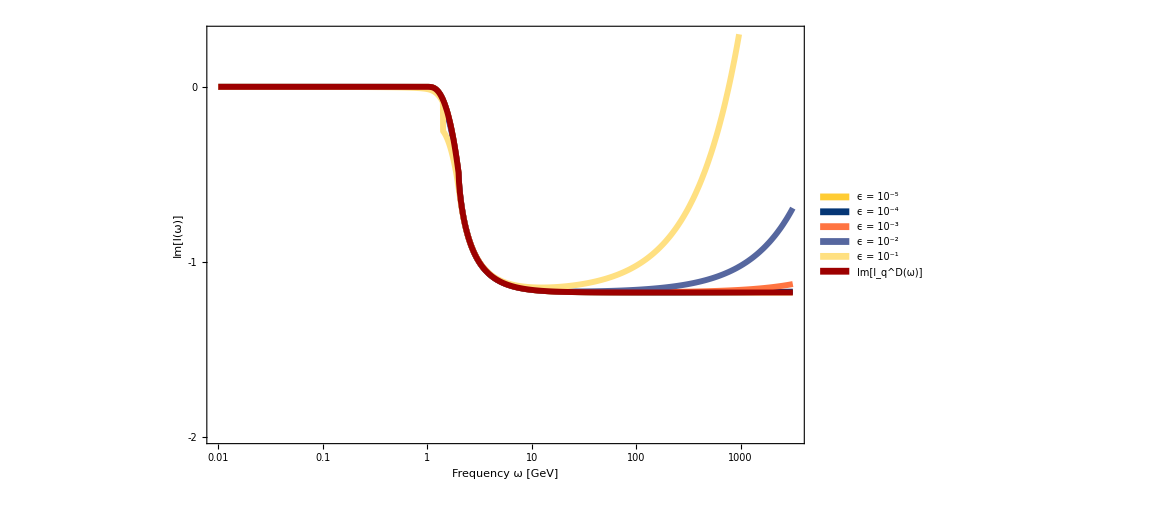

```mathematica
ImContCheck = With[{ε=10^Range[-5,-1]},LogLinearPlot[{Evaluate[Im[IVecRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε],Im[IVecRen[ω,22/100,1,1,2]]
},{ω,10^-2,10^3.5},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-2, 10^3.5},yRange={-1.99,0.3}},
PlotStyle->{Directive[clearPlotColors[[5]],Thickness[0.005]], Directive[clearPlotColors[[4]],Thickness[0.005]], Directive[clearPlotColors[[3]],Thickness[0.005]], Directive[clearPlotColors[[2]],Thickness[0.005]] ,Directive[clearPlotColors[[1]],Thickness[0.005]],Directive[MScRed,Thickness[0.005]] }, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Frequency ω [GeV]", "  Im[I(ω)] "},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{ clearPlotColors[[5]],clearPlotColors[[4]],clearPlotColors[[3]],clearPlotColors[[2]],clearPlotColors[[1]],MScRed},{"ϵ = 10^-5", "ϵ = 10^-4", "ϵ = 10^-3", "ϵ = 10^-2", "ϵ = 10^-1", "Im[I_q^D(ω)]"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.04,.82}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]]
exportFigure[ImContCheck];
```

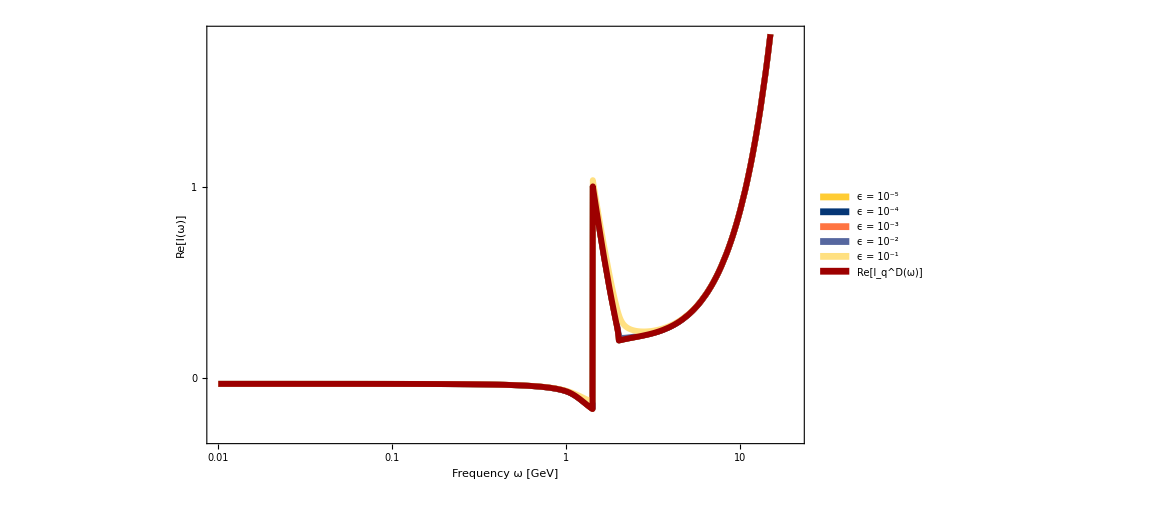

```mathematica
ReContCheck = With[{ε=10^Range[-5,-1]},LogLinearPlot[{Evaluate[Re[IVecRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε],Re[IVecRen[ω,22/100,1,1,2]]
},{ω,10^-2,10^3.5},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-2, 2*10^1},yRange={-0.3,1.8}},
PlotStyle->{Directive[clearPlotColors[[5]],Thickness[0.005]], Directive[clearPlotColors[[4]],Thickness[0.005]], Directive[clearPlotColors[[3]],Thickness[0.005]], Directive[clearPlotColors[[2]],Thickness[0.005]] ,Directive[clearPlotColors[[1]],Thickness[0.005]],Directive[MScRed,Thickness[0.005]] }, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Frequency ω [GeV]", "  Re[I(ω)] "},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{ clearPlotColors[[5]],clearPlotColors[[4]],clearPlotColors[[3]],clearPlotColors[[2]],clearPlotColors[[1]],MScRed},{"ϵ = 10^-5", "ϵ = 10^-4", "ϵ = 10^-3", "ϵ = 10^-2", "ϵ = 10^-1", "Re[I_q^D(ω)]"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.04,0.94}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]]
exportFigure[ReContCheck];
```

#### BPHZ Renormalization

```mathematica
α[p_,λA_,λ_] := {-2,-(p^2+λ^2-4 λA^2)/λA^2,(3 p^2)/λA^2}
β[p_,λA_,λ_] :={0,-(p^2+λ^2)/λA^2,(3 p^2)/λA^2}
```

```mathematica
f0[p_,λA_,λ_] := -2+Log[λ]+1/p^2(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+(-λ^2+λA^2) Log[λ/λA])+Log[λA]
g0[p_,λA_,λ_] := -2+(λ^2 Log[1+p^2/λ^2])/p^2+Log[p^2+λ^2]
f1[p_,λA_,λ_] := 1/(4 p^4)(-4 p^4-2 p^2 λ^2+2 p^2 λA^2+2 (p^4-2 p^2 λ^2-(λ^2-λA^2)^2) Log[λ]+2 p^4 Log[λA]+4 p^2 λ^2 Log[λA]+2 λ^4 Log[λA]-4 λ^2 λA^2 Log[λA]+2 λA^4 Log[λA]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])
g1[p_,λA_,λ_] := (-(2 p^2+λ^2) (p^2+2 λ^2 Log[λ])+(p^2+λ^2)^2 Log[p^2+λ^2])/(2 p^4)
f2[p_,λA_,λ_] := 1/(18 p^6)(-13 p^6-15 p^4 λ^2-6 p^2 λ^4+3 p^4 λA^2+12 p^2 λ^2 λA^2-6 p^2 λA^4+6 (p^6-3 p^4 λ^2-(λ^2-λA^2)^3-3 p^2 (λ^4-λ^2 λA^2)) Log[λ]+6 p^6 Log[λA]+18 p^4 λ^2 Log[λA]+18 p^2 λ^4 Log[λA]+6 λ^6 Log[λA]-18 p^2 λ^2 λA^2 Log[λA]-18 λ^4 λA^2 Log[λA]+18 λ^2 λA^4 Log[λA]-6 λA^6 Log[λA]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])
g2[p_,λA_,λ_] := -(13 p^6+15 p^4 λ^2+6 p^2 λ^4+12 (3 p^4 λ^2+3 p^2 λ^4+λ^6) Log[λ]-6 (p^2+λ^2)^3 Log[p^2+λ^2])/(18 p^6)
```

```mathematica
f[p_,λA_,λ_] := {f0[p,λA,λ],f1[p,λA,λ],f2[p,λA,λ]}
g[p_,λA_,λ_] := {g0[p,λA,λ],g1[p,λA,λ],g2[p,λA,λ]}
```

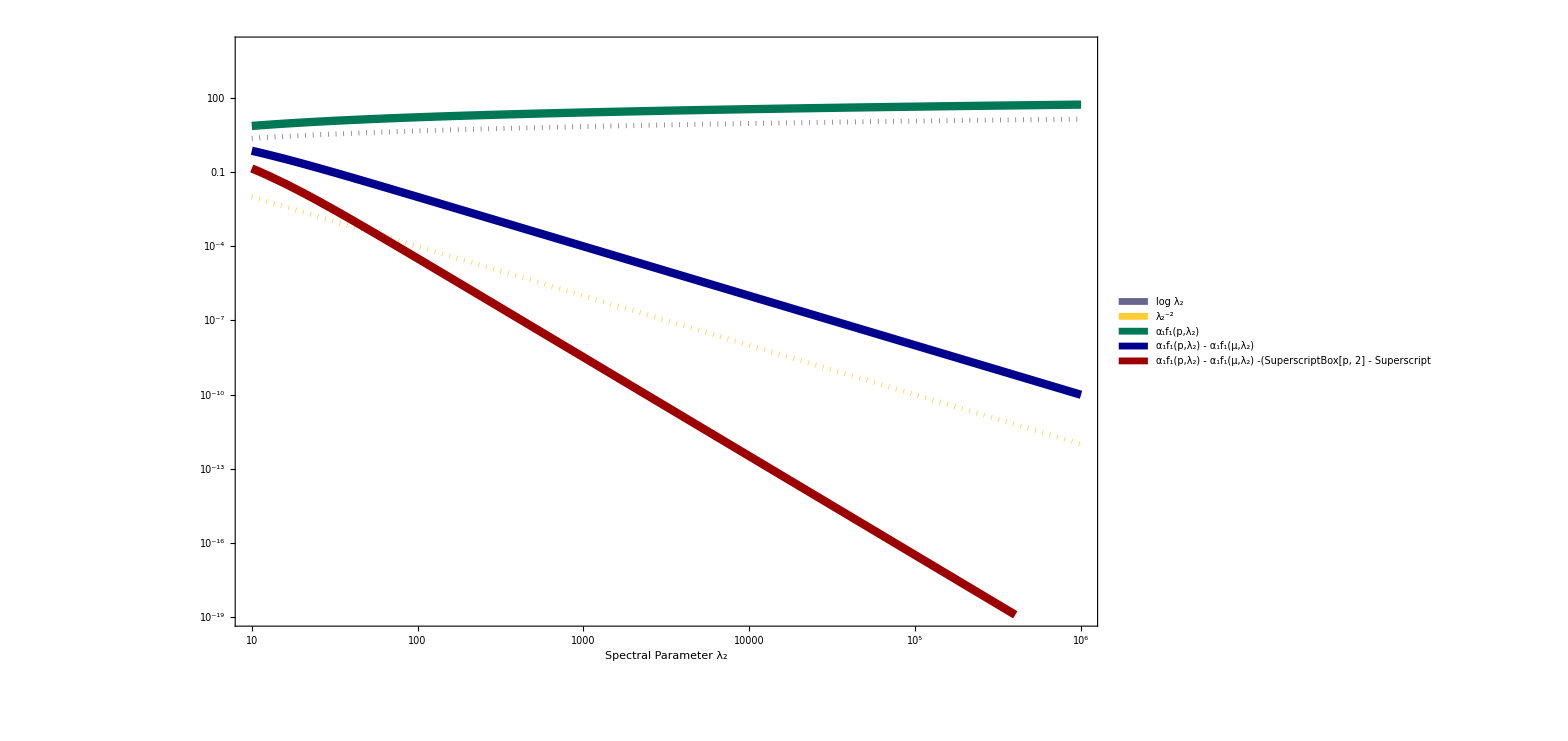

```mathematica
FiniteIntegrands1 =With[{λA=1, μ=10,pEval=1, i=1},LogLogPlot[{ Log[λ], λ^-2,Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]]],Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]],Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[α[q,λA,λ][[i]]f[q, λA,λ][[i]],q]/.{q->μ})]},{λ,10^1,10^6},
WorkingPrecision->100,
ImageSize->1200,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^1, 10^6},yRange={10^-18.9,10^4}},
PlotStyle->{Directive[MScGray,Thickness[0.003], Dotted],Directive[clearPlotColors[[5]],Thickness[0.003], Dotted], Directive[MScGreen,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]] ,Directive[MScRed,Thickness[0.005]] }, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->{FontFamily->"Palatino",FontSize->45},
FrameLabel->{"Spectral Parameter λ_2 ", "  "},
FrameTicks->{{LogTicks[Sequence@@yRange, ShowMinorTicks->False,LogPlot->True,TickLabelStep->5],LogTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False,LogPlot->True]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{  MScGray,clearPlotColors[[5]],MScGreen,MScBlue,MScRed},{"log λ_2", "λ_2^-2", "α_1f_1(p,λ_2)", "α_1f_1(p,λ_2) - α_1f_1(μ,λ_2)", "α_1f_1(p,λ_2) - α_1f_1(μ,λ_2) -(SuperscriptBox[p, 2] - SuperscriptBox[μ, 2])/(2  μ)D[α_1f_1(μ,λ_2)]"}, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",40}],
{Scaled[{0.04,0.6}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]]
exportFigure[FiniteIntegrands1];
```

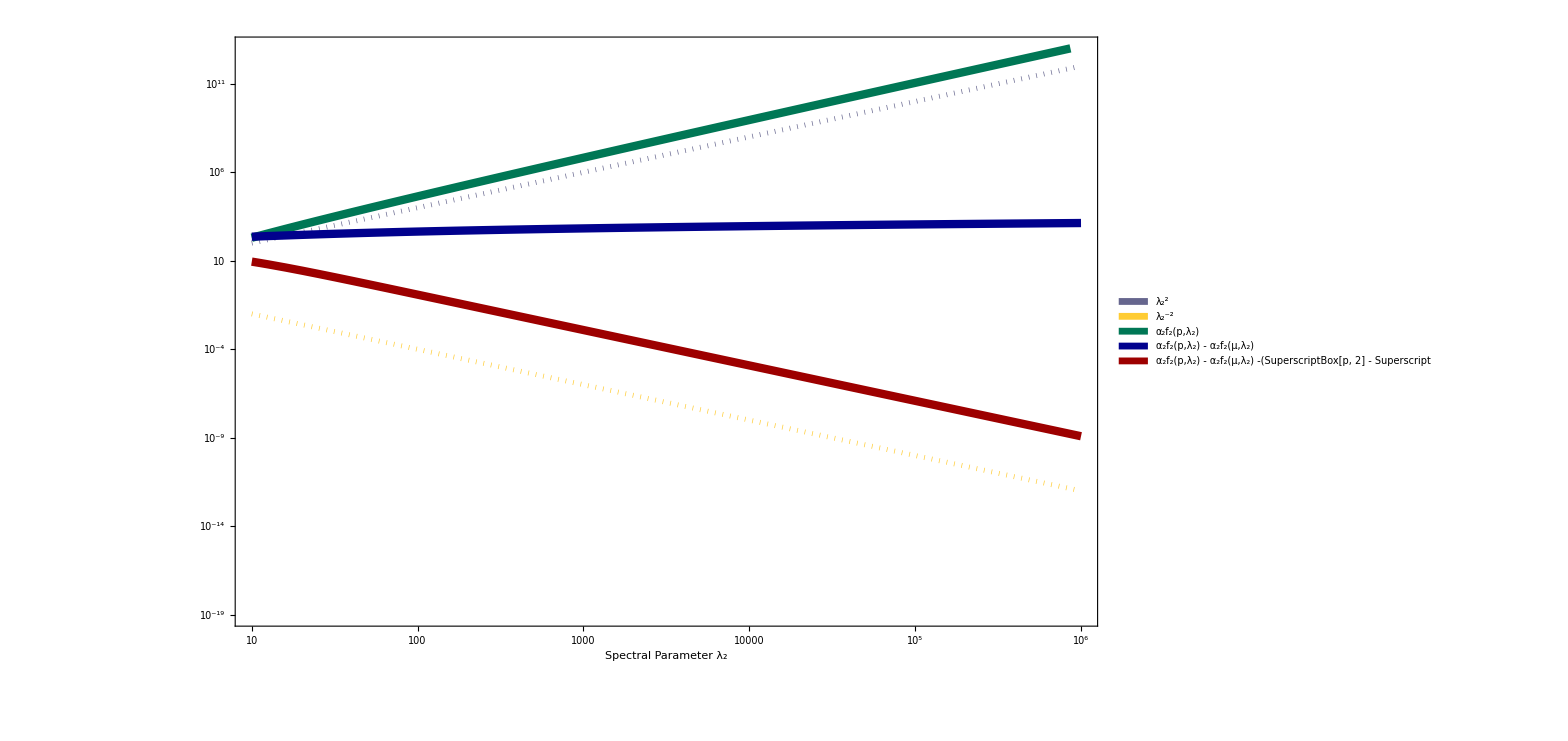

```mathematica
FiniteIntegrands2 =With[{λA=1, μ=10,pEval=1, i=2},LogLogPlot[{  λ^2, λ^-2,Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]]],Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]],Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[α[q,λA,λ][[i]]f[q, λA,λ][[i]],q]/.{q->μ})]},{λ,10^1,10^6},
WorkingPrecision->100,
ImageSize->1200,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^1, 10^6},yRange={10^-19,10^13}},
PlotStyle->{Directive[MScGray,Thickness[0.003], Dotted],Directive[clearPlotColors[[5]],Thickness[0.003], Dotted], Directive[MScGreen,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]] ,Directive[MScRed,Thickness[0.005]] }, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->{FontFamily->"Palatino",FontSize->45},
FrameLabel->{"Spectral Parameter λ_2 ", "  "},
FrameTicks->{{LogTicks[Sequence@@yRange, ShowMinorTicks->False,LogPlot->True,TickLabelStep->5,ShowFirst-> False ,ShowLast-> False],LogTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False,LogPlot->True]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{  MScGray,clearPlotColors[[5]],MScGreen,MScBlue,MScRed},{"λ_2^2", "λ_2^-2", "α_2f_2(p,λ_2)", "α_2f_2(p,λ_2) - α_2f_2(μ,λ_2)", "α_2f_2(p,λ_2) - α_2f_2(μ,λ_2) -(SuperscriptBox[p, 2] - SuperscriptBox[μ, 2])/(2  μ)D[α_2f_2(μ,λ_2)]"}, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",40}],
{Scaled[{0.04,0.6}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]]
exportFigure[FiniteIntegrands2];
```

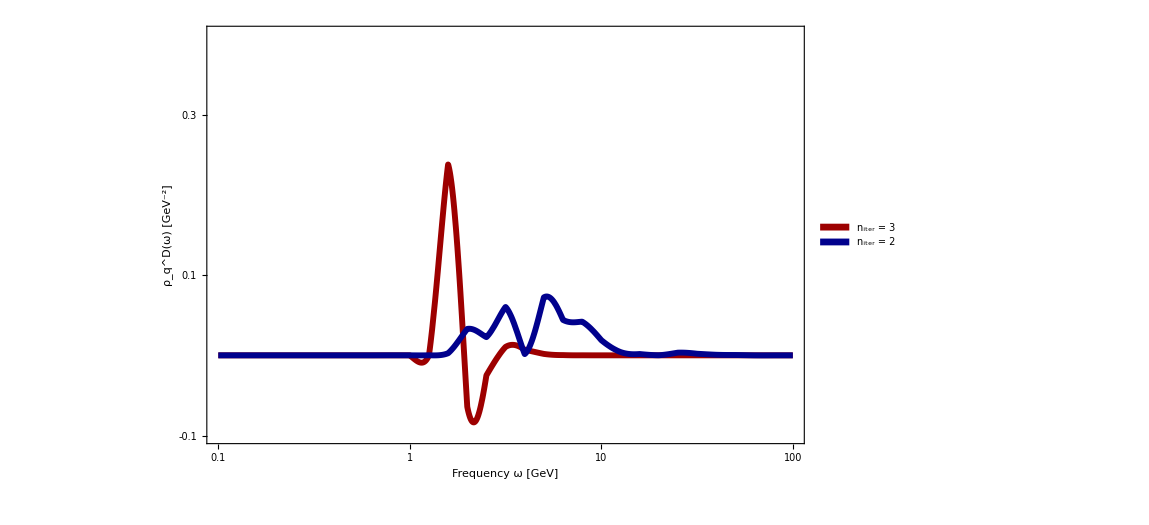

```mathematica
LogLinearPlot[{Interpolation[SpecFuncsρ2[[3]]][ω], Interpolation[SpecFuncsρ1[[2]]][ω]},{ω,10^-1,10^2},
ImageSize->850,Frame->True,Axes->None,Exclusions-> None,
PlotRange->{xRange={10^-1,10^2},yRange={-0.1,0.4}},
PlotStyle->{Directive[MScRed,Thickness[0.005]], Directive[MScBlue,Thickness[0.005]]}, 
FrameStyle->Directive[Black,Thickness[0.005]],
LabelStyle->MScFont,
FrameLabel->{"Frequency ω [GeV]", "  ρ_q^D(ω) [GeV^-2]"},
FrameTicks->{{LinTicks[Sequence@@yRange, ShowMinorTicks->False,TickLabelStep->2],LinTicks[Sequence@@yRange,ShowTickLabels->False,ShowMinorTicks->False]},{LogTicks[Sequence@@xRange,ShowMinorTicks->True,LogPlot->True],LogTicks[Sequence@@xRange,ShowTickLabels->False,ShowMinorTicks->True,LogPlot->True]}},
FrameStyle->{{Directive[Thick,Black],Directive[Thick,Black]},{Directive[Thick,Black], Directive[Thick,Black]}},
PlotLegends->Placed[SwatchLegend[{MScRed, MScBlue},{"n_iter = 3", "n_iter = 2"}, LegendFunction->Framed, LegendMarkerSize->{20,10},LabelStyle->{FontFamily->"Palatino",35}],
{Scaled[{0.7,.93}],{0,1}}](*,
Epilog->Inset[watermark,Automatic,Automatic,Automatic,{1,1}]*)
]
```

```mathematica
ListPlot[λA, NIntegrate[quarkSEVecReg[ω,αs,λA,λ,ρATmp,ρ1Tmp],{λA,λAmin,λAmax},{λ,λmin,λmax},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3]},{ω,momRange}]
```